# Multi Atom Liouville Equation Generator

## Abstract

The MultiAtomLiouvilleEquationGenerator is a Mathematica package that ...

## Content

Multi Atom Liouville Equation Generator
Abstract
Content
Loading MultiAtomLiouvilleEquationGenerator
Functions
AdjointMasterEquation
CleanUp
DipoleMatrixElement
ExpectationValue
FilteredClebschGordan
Ham
HamDressed
InitialConditions
LiouvilleAdjointMasterEquation
LiouvilleCommutator
LiouvilleDaggerLindbladianFromLindbladOperators
LiouvilleLindbladian
LiouvilleLindbladianDagger
LiouvilleLindbladianFromLindbladOperators
LiouvilleMasterEquation
MasterEquation
MultiAtomBasis
Proj
RotatingFrameParms
RotatingFrameTrans
Sigma
SigmaT
Sigmaz
TransitionLists
Examples
A single two-level atom
Two two-level atoms
Five two-level atoms
Optical pumping
Superradiance
The dressed state evolution operator
Time evolution of transmons

## Loading MultiAtomLiouvilleEquationGenerator

To load the MultiAtomLiouvilleEquationGenerator, write:

SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs[“MultiAtomLiouvilleEquationGenerator`”]

Set the path to the MultiAtomLiouvilleEquationGenerator package and load

```mathematica
PathToMultiAtomLiouvilleEquationGenerator="/Users/akb/Dropbox/Trabajo/Rubidio/Project008";
```

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

"Content"

# Functions

These are the functions

## MultiAtomBasis

MultiAtomBasis[na, nl] : na, nl ∈ Integers
Returns a SparseArray containing a multi atom basis for na atoms with nl quantum levels each.

"Content"

#### Example

Generate a matrix basis for two atoms with two quantum levels each

```mathematica
h = MultiAtomBasis[2,2]
```

SparseArray[…]

Show that the basis elements are orthonormal

```mathematica
Table[Tr[el1.el2],{el1,h},{el2,h}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Generate a matrix basis for two atoms with four quantum levels

```mathematica
h = MultiAtomBasis[2,4]
```

SparseArray[…]

## Sigma

Sigma[tr,α, nl, na] : tr={tr_1,tr_2}; tr_1, tr_2, α, na, nl ∈ Ingeters
Returns a SparseArray with the jump operator |tr_1⟩⟨tr_2| between states |tr_1⟩ and |tr_2⟩ for the α-th atom of a system consisting of na atoms with nl quantum levels.

"Content"

#### Example

Generate a the jump operator |1⟩⟨2| (t r = {1,2}) for the first atom (α=1) in a two level (nl=2)  three atom (na=3) system

```mathematica
σ=Sigma[{1,2},1,2,3]
```

SparseArray[…]

The corresponding matrix is given by

```mathematica
σ//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## SigmaT

SigmaT[tr,α, nl, na] : tr={tr_1,tr_2}; tr_1, tr_2, α, na, nl ∈ Ingeters
Returns a SparseArray with the adjoint jump operator |tr_2⟩⟨tr_1| between states |tr_1⟩ and |tr_2⟩ for the α-th atom of a system consisting of na atoms with nl quantum levels.

"Content"

#### Example

Generate a the adjoint jump operator |2⟩⟨1| (t r = {1,2}) for the first atom (α=1) in a two level (nl=2)  three atom (na=3) system

```mathematica
σt=SigmaT[{1,2},1,2,3]
```

SparseArray[…]

The corresponding matrix is given by

```mathematica
σt//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

## Sigmaz

Sigmaz[tr,α, nl, na] : tr={tr_1,tr_2}; tr_1, tr_2, α, na, nl ∈ Ingeters
Returns a SparseArray with the Pauli σ_z-like operator |tr_1⟩⟨tr_1| - |tr_2⟩⟨tr_2| of states |tr_1⟩ and |tr_2⟩ for the α-th atom of a system consisting of na atoms with nl quantum levels.

"Content"

#### Example

Generate a the σ_z-like operator |1⟩⟨1| -  |2⟩⟨2| (t r = {1,2}) for the first atom (α=1) in a two level (nl=2)  three atom (na=3) system

```mathematica
σz=Sigmaz[{1,2},1,2,3]
```

SparseArray[…]

The corresponding matrix is given by

```mathematica
σz//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

## Proj

Proj[h, Op]: h, Op ∈ SparseArray
Returns a SparseArray of dimension Length[h] = Length[Op] that contains the expansion coefficients Op_i of the operator Op given by Op_i = Tr[h_i Op] where h is the matrix basis.

"Content"

#### Examples

Calculate the expansion coefficients of the operator

```mathematica
Op = SparseArray[{{1,1}->1,{3,3}->1},4];
MatrixForm[Op]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

A suitable matrix basis to expand this operator is the one formed by all possible 4×4 matrices

```mathematica
h = MultiAtomBasis[2,2]
```

SparseArray[…]

The coefficients of the projection of Op onto the basis h is thus

```mathematica
Normal[Proj[h,Op]]
```

{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

## ExpectationValue

ExpectationValue[h, q, Op]: h, q, Op ∈ SparseArray
Returns an expression for the expectation value ∑_i Tr[h_i Op]q_i of the operator Op where q_i =Tr[h_iρ] are the density matrix coefficients and h is the matrix basis.

"Content"

#### Example

```mathematica
h = MultiAtomBasis[2,2]
dim=Length[h]
rho=SparseArray[Table[Subscript[ρ,ii],{ii,1,dim}]]
Op = SparseArray[{{1,1}->1,{3,3}->1},4]
```

SparseArray[…]

16

SparseArray[…]

SparseArray[…]

```mathematica
ExpectationValue[h, rho, Op]
```

ρ_1+ρ_5

## Ham

Ham[transCE, transdd, nl,  na, t] : transCE, trasdd ∈ List;  na, nl ∈ Ingeters, t is a Mathematica symbol that represents the time variable
Returns a SparseArray for the time-dependent Hamiltonian in the interaction picture that accounts for light-matter and dipole-dipole interactions. The variable  transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …} contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser ql_(k,1)and ql_(k,2), the Rabi parameter Rb_k, the detuning  Δ_k and the phase ϕ_k.  The variable transdd={{tr_(1,1), tr_(1,2)}, α_1, β_1, Ω_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2, β_2, Ω_2 ,δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions corresponding to the two distinct α_k-th and β_k-th atoms (α_k≠ β_k). The strength of the interaction is given by Ω_k. δ_k is the detuning between these two transitions. For δ_k to be significant, it must be much smaller than both energy transitions themselves. Usually δ_k=0. transCE and transdd might be empty lists in case there are no light-matter interactions or/and there are no dipole-dipole interactions.

"Content"

#### Example

Generate the Hamiltonian for a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

Assuming that the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩ have different energy differences and, therefore, do not interact among themselves, the trandd parameter is given by

```mathematica
transdd=transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{2,3}, {2,3},1,2,Subscript[Ω, 2],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0},{{2,3}, {2,3},2,1,Subscript[Ω, 2],0}};
```

The Hamiltonian is generated with

```mathematica
ham=Ham[transCE, transdd, 3, 2, t]
```

SparseArray[…]

```mathematica
ham//MatrixForm
```

(0 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0 | 0 | 0 | 0 | 0
-ⅇ^(ⅈ t Δ_1) R_1 | 0 | -ⅇ^(ⅈ (ϕ-t Δ_2)) R_2 | Ω_1 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0 | 0 | 0 | 0
0 | -ⅇ^(ⅈ (-ϕ+t Δ_2)) R_2 | 0 | 0 | 0 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0 | 0 | 0
-ⅇ^(ⅈ t Δ_1) R_1 | Ω_1 | 0 | 0 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0 | -ⅇ^(ⅈ (ϕ-t Δ_2)) R_2 | 0 | 0
0 | -ⅇ^(ⅈ t Δ_1) R_1 | 0 | -ⅇ^(ⅈ t Δ_1) R_1 | 0 | -ⅇ^(ⅈ (ϕ-t Δ_2)) R_2 | 0 | -ⅇ^(ⅈ (ϕ-t Δ_2)) R_2 | 0
0 | 0 | -ⅇ^(ⅈ t Δ_1) R_1 | 0 | -ⅇ^(ⅈ (-ϕ+t Δ_2)) R_2 | 0 | 0 | Ω_2 | -ⅇ^(ⅈ (ϕ-t Δ_2)) R_2
0 | 0 | 0 | -ⅇ^(ⅈ (-ϕ+t Δ_2)) R_2 | 0 | 0 | 0 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0
0 | 0 | 0 | 0 | -ⅇ^(ⅈ (-ϕ+t Δ_2)) R_2 | Ω_2 | -ⅇ^(ⅈ t Δ_1) R_1 | 0 | -ⅇ^(ⅈ (ϕ-t Δ_2)) R_2
0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ (-ϕ+t Δ_2)) R_2 | 0 | -ⅇ^(ⅈ (-ϕ+t Δ_2)) R_2 | 0)

## HamDressed

HamDressed[transCE, transdd, nl,  na] : transCE, trasdd ∈ List;  na, nl ∈ Ingeters
Returns a SparseArray for the time-independent Hamiltonian in the dressed state base that accounts for light-matter and dipole-dipole interactions. The variable  transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …} contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser ql_(k,1)and ql_(k,2), the Rabi parameter Rb_k, the detuning  Δ_k and the phase ϕ_k.  The variable transdd={{tr_(1,1), tr_(1,2)}, α_1, β_1, Ω_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2, β_2, Ω_2 ,δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions corresponding to the two distinct α_k-th and β_k-th atoms (α_k≠ β_k). The strength of the interaction is given by Ω_k. δ_k is the detuning between these two transitions. For HamDressed these parameters must be δ_k=0, otherwise the Hamiltonian becomes time-dependent. transCE and transdd might be empty lists in case there are no light-matter interactions or/and there are no dipole-dipole interactions.

"Content"

#### Example

Generate the Hamiltonian for a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

Assuming that the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩ have different energy differences and, therefore, do not interact among themselves, the trandd parameter is given by

```mathematica
transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{2,3}, {2,3},1,2,Subscript[Ω, 2],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0},{{2,3}, {2,3},2,1,Subscript[Ω, 2],0}};
```

The Hamiltonian is generated with

```mathematica
hamd=HamDressed[transCE, transdd, 3, 2]
```

SparseArray[…]

```mathematica
SparseArray[hamd//Normal//Simplify]//MatrixForm
```

(-2/3 (2 Δ_1+Δ_2) | -R_1 | 0 | -R_1 | 0 | 0 | 0 | 0 | 0
-R_1 | 1/3 (-Δ_1-2 Δ_2) | -ⅇ^(ⅈ ϕ) R_2 | Ω_1 | -R_1 | 0 | 0 | 0 | 0
0 | -ⅇ^(-ⅈ ϕ) R_2 | 1/3 (-Δ_1+Δ_2) | 0 | 0 | -R_1 | 0 | 0 | 0
-R_1 | Ω_1 | 0 | 1/3 (-Δ_1-2 Δ_2) | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | 0
0 | -R_1 | 0 | -R_1 | 2/3 (Δ_1-Δ_2) | -ⅇ^(ⅈ ϕ) R_2 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0
0 | 0 | -R_1 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 1/3 (2 Δ_1+Δ_2) | 0 | Ω_2 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 1/3 (-Δ_1+Δ_2) | -R_1 | 0
0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | Ω_2 | -R_1 | 1/3 (2 Δ_1+Δ_2) | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 2/3 (Δ_1+2 Δ_2))

## RotatingFrameParms

RotatingFrameParms[transCE] : transCE ∈ List
Returns a List of the rotation parameters {μ_1, μ_2, …μ_n }, where n=Length[transCE], necessary to transform the time-dependent Hamiltonian Ham into the time-independent HamDressed by switching to a rotating frame. The variable  transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …} contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser ql_(k,1)and ql_(k,2), the Rabi parameter Rb_k, the detuning  Δ_k and the phase ϕ_k. The dressed Hamiltonian (HamDressed) is obtained from the time-dependent Hamiltonian (Ham) as H_D=U_1U_2…U_nHU_n^†…U_2^†U_1^† where H is the Hamiltonian given by Ham, H_D is the Hamiltonian given by HamDressed, U_k=MatrixExp[-ⅈ t μ_kσ_(z,k)] and σ_(z,k) = Sigmaz[transCE[[k,1]], α_k, nl, na]. nl and na are the numbers of quantum states and atoms, respectively.

"Content"

#### Example

Generate the rotation parameters to remove the time dependence of the Hamiltonian for a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

```mathematica
μ=RotatingFrameParms[transCE]
```

{1/3 (-2 Δ_1-Δ_2),1/3 (-2 Δ_1-Δ_2),1/3 (-Δ_1-2 Δ_2),1/3 (-Δ_1-2 Δ_2)}

These parameters correspond to the following four transformations

```mathematica
U1=MatrixExp[-ⅈ t μ[[1]]Sigmaz[transCE[[1,1]],1,3,2]];
U2=MatrixExp[-ⅈ t μ[[2]]Sigmaz[transCE[[2,1]],2,3,2]];
U3=MatrixExp[-ⅈ t μ[[3]]Sigmaz[transCE[[3,1]],1,3,2]];
U4=MatrixExp[-ⅈ t μ[[4]]Sigmaz[transCE[[4,1]],2,3,2]];
U1t=MatrixExp[ⅈ t μ[[1]]Sigmaz[transCE[[1,1]],1,3,2]];
U2t=MatrixExp[ⅈ t μ[[2]]Sigmaz[transCE[[2,1]],2,3,2]];
U3t=MatrixExp[ⅈ t μ[[3]]Sigmaz[transCE[[3,1]],1,3,2]];
U4t=MatrixExp[ⅈ t μ[[4]]Sigmaz[transCE[[4,1]],2,3,2]];
```

These transformations remove the time-dependence from the Hamiltonian ham obtained in the previous examples

```mathematica
U1.U2.U3.U4.ham.U4t.U3t.U2t.U1t//Simplify//MatrixForm
```

(0 | -R_1 | 0 | -R_1 | 0 | 0 | 0 | 0 | 0
-R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | Ω_1 | -R_1 | 0 | 0 | 0 | 0
0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 0 | -R_1 | 0 | 0 | 0
-R_1 | Ω_1 | 0 | 0 | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | 0
0 | -R_1 | 0 | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0
0 | 0 | -R_1 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | Ω_2 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 0 | -R_1 | 0
0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | Ω_2 | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0)

The dressed Hamiltonian hamd of the previous examples is recovered by adding the effective Hamiltonian - ⅈ ∑_k U_kd/dtU_k^†

```mathematica
(U1.U2.U3.U4.ham.U4t.U3t.U2t.U1t- ⅈ(U1.D[U1t,t]+U2.D[U2t,t]+U3.D[U3t,t]+U4.D[U4t,t]))//Normal//Simplify//MatrixForm
```

(-2/3 (2 Δ_1+Δ_2) | -R_1 | 0 | -R_1 | 0 | 0 | 0 | 0 | 0
-R_1 | 1/3 (-Δ_1-2 Δ_2) | -ⅇ^(ⅈ ϕ) R_2 | Ω_1 | -R_1 | 0 | 0 | 0 | 0
0 | -ⅇ^(-ⅈ ϕ) R_2 | 1/3 (-Δ_1+Δ_2) | 0 | 0 | -R_1 | 0 | 0 | 0
-R_1 | Ω_1 | 0 | 1/3 (-Δ_1-2 Δ_2) | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | 0
0 | -R_1 | 0 | -R_1 | 2/3 (Δ_1-Δ_2) | -ⅇ^(ⅈ ϕ) R_2 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0
0 | 0 | -R_1 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 1/3 (2 Δ_1+Δ_2) | 0 | Ω_2 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 1/3 (-Δ_1+Δ_2) | -R_1 | 0
0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | Ω_2 | -R_1 | 1/3 (2 Δ_1+Δ_2) | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 2/3 (Δ_1+2 Δ_2))

## RotatingFrameTrans

RotatingFrameTrans[transCE, nl, na, t] : transCE ∈ List, nl, na ∈ Integers, t is a Mathematica symbol that represents the time variable
RotatingFrameTrans[h, transCE, nl, na, t] : h ∈ SparseArray, transCE ∈ List, nl, na ∈ Integers, t is a Mathematica symbol that represents the time variable
If the basis h is not provided, the function returns a List of two SparseArray objects:{U_R, U_R^†}, where U_R is the transformation that removes the time dependence from the time-dependent Hamiltonian Ham by switching to a rotating frame. The transformation U_R  is composed of the n=Length[transCE] rotations, each arising  from  the parameters μ = {,μ_1, μ_2, …, μ_n} produced by RotatingFrameParms. Thus, U_R=U_1U_2…U_n where each U_k=MatrixExp[-ⅈ t μ_kσ_(z,k)],  with μ_k=μ[[k]], and σ_(z,k) = Sigmaz[transCE[[k,1]], α_k, nl, na]. If the basis h is given, RotatingFramTrans returns a List of four SparseArray objects  {U_R, U_R^†, L_R, L_R^†} where L_R and L_R^† are the superoperators corresponding to the linear maps L_Rρ =U_Rρ U_R^† and   L_R^†ρ =U_R^†ρ U_R. These superoperators are useful for transforming other superoperators into and out of the rotating frame. The variable transCE is structured as transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …}. This list contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser (ql_(k,1)and ql_(k,2)), the Rabi frequency Rb_k, the detuning  Δ_k and the phase ϕ_k.

"Content"

#### Example

Generate the transformations to transform the Hamiltonian for a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

This gives rise to the following transformations

```mathematica
U=RotatingFrameTrans[transCE, 3, 2, t]
```

{SparseArray[…],SparseArray[…]}

These rotations shift the Hamiltonian ham of previous examples into a rotating frame in which it becomes time-independent

```mathematica
U[[1]].ham.U[[2]]//Normal//Simplify//MatrixForm
```

(0 | -R_1 | 0 | -R_1 | 0 | 0 | 0 | 0 | 0
-R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | Ω_1 | -R_1 | 0 | 0 | 0 | 0
0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 0 | -R_1 | 0 | 0 | 0
-R_1 | Ω_1 | 0 | 0 | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | 0
0 | -R_1 | 0 | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0
0 | 0 | -R_1 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | Ω_2 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 0 | -R_1 | 0
0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | Ω_2 | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0)

The dressed Hamiltonian hamd of the previous examples is recovered by adding the effective Hamiltonian - ⅈ U_Rd/dtU_R^†

```mathematica
(U[[1]].ham.U[[2]]-ⅈ U[[1]].D[U[[2]],t])//Normal//Simplify//MatrixForm
```

(-2/3 (2 Δ_1+Δ_2) | -R_1 | 0 | -R_1 | 0 | 0 | 0 | 0 | 0
-R_1 | 1/3 (-Δ_1-2 Δ_2) | -ⅇ^(ⅈ ϕ) R_2 | Ω_1 | -R_1 | 0 | 0 | 0 | 0
0 | -ⅇ^(-ⅈ ϕ) R_2 | 1/3 (-Δ_1+Δ_2) | 0 | 0 | -R_1 | 0 | 0 | 0
-R_1 | Ω_1 | 0 | 1/3 (-Δ_1-2 Δ_2) | -R_1 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0 | 0
0 | -R_1 | 0 | -R_1 | 2/3 (Δ_1-Δ_2) | -ⅇ^(ⅈ ϕ) R_2 | 0 | -ⅇ^(ⅈ ϕ) R_2 | 0
0 | 0 | -R_1 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 1/3 (2 Δ_1+Δ_2) | 0 | Ω_2 | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | 0 | 1/3 (-Δ_1+Δ_2) | -R_1 | 0
0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | Ω_2 | -R_1 | 1/3 (2 Δ_1+Δ_2) | -ⅇ^(ⅈ ϕ) R_2
0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 0 | -ⅇ^(-ⅈ ϕ) R_2 | 2/3 (Δ_1+2 Δ_2))

## LiouvilleLindbladian

LiouvilleLindbladian[h, transLi, nl, na] : h ∈ SparseArray, transLi ∈ List, nl, na ∈ Integers
LiouvilleLindbladian[h, transLi, nl, na, t] : h ∈ SparseArray, transLi ∈ List, nl, na ∈ Integers, t is a Mathematica symbol that represents the time variable
Returns a SparseArray of dimension  Length[h] that contains the Liouville superoperator corresponding to the Lindbladian of the master equation.  na and nl are the numbers of atoms and quantum levels of the system. h is the SparseArray that contains the matrix basis generated with MultiAtomBasis.The variable transLi = {{tr_(1,1), tr_(1,2)}, α_1,  β_1,  γ_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2,  β_2, γ_2 , δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions ql_(k,1,1)→ ql_(k,1,2) (between the quantum levels tagged as ql_(k,1,1) and ql_(k,1,2)) and ql_(k,2,1)→ ql_(k,2,2) (between the quantum levels tagged as ql_(k,2,1) and ql_(k,2,2)) of the two distinct α_k-th and β_k-th atoms. The strength of the interaction is given by γ_k. δ_k is the detuning between these two transitions. These usually vanish, i.e. δ_k=0. In this case, the time variable t can be omitted as an argument of LiouvilleLindbladian.

"Content"

#### Example

Calculate the Liouville superoperator corresponding to the Lindbladian part of the master equation of a system of two (na=2) three level (nl=3) atoms. The only  transitions with non-vanishing dipole matrix elements are  |1⟩ →|2⟩ and |2⟩ →|3⟩. The transition  |1⟩ →|2⟩ is tagged with the number 1, and the transition  |2⟩ →|3⟩ is tagged with the number 2. The strength of the dipole couplings are tagged accordingly: γ_1 is the coupling due to the dipole element of the transition 1 if only one atom is involved, γ_(1,1) is the coupling due to the dipole element of the transition 1 if two different atoms are involved,  γ_2 is the coupling due to the dipole element of the transition 2 if only one atom is involved and γ_(2,2) is the coupling due to the dipole element of the transition 2 if two different atoms are involved.

Generate the matrix basis por two atoms (na=2) with three levels (nl=3)

```mathematica
h = MultiAtomBasis[3,2]
```

SparseArray[…]

Define the variable transLi.

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0},{{1,2},{1,2},2,2,Subscript[γ, 1],0},{{1,2},{1,2},1,2,Subscript[γ, 1,1],0},{{1,2},{1,2},2,1,Subscript[γ, 1,1],0},{{2,3},{2,3},1,1,Subscript[γ, 2],0},{{2,3},{2,3},2,2,Subscript[γ, 2],0},{{1,2},{1,2},1,2,Subscript[γ, 2,2],0},{{1,2},{1,2},2,1,Subscript[γ, 2,2],0}};
```

Notice that, in contrast with the variable transdd where α_k≠β_k, for the variable transLIin some of the terms α_k=β_k.

```mathematica
LiouvilleL=LiouvilleLindbladian[h, transLi,3,2]
```

SparseArray[…]

## LiouvilleLindbladianDagger

LiouvilleLindbladianDagger[h, transLi, nl, na] : h ∈ SparseArray, transLi ∈ List, nl, na ∈ Integers
LiouvilleLindbladianDagger[h, transLi, nl, na, t] : h ∈ SparseArray, transLi ∈ List, nl, na ∈ Integers, t is a Mathematica symbol that represents the time variable
Returns a SparseArray of dimension  Length[h] that contains the adjoint Liouville superoperator corresponding to the adjoint Lindbladian of the adjoint master equation.  na and nl are the numbers of atoms and quantum levels of the system. h is the SparseArray that contains the matrix basis generated with MultiAtomBasis.The variable transLi = {{tr_(1,1), tr_(1,2)}, α_1,  β_1,  γ_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2,  β_2, γ_2 , δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions ql_(k,1,1)→ ql_(k,1,2) (between the quantum levels tagged as ql_(k,1,1) and ql_(k,1,2)) and ql_(k,2,1)→ ql_(k,2,2) (between the quantum levels tagged as ql_(k,2,1) and ql_(k,2,2)) of the two distinct α_k-th and β_k-th atoms. The strength of the interaction is given by γ_k. δ_k is the detuning between these two transitions. These usually vanish, i.e. δ_k=0. In this case, the time variable t can be omitted as an argument of LiouvilleLindbladianDagger.

"Content"

#### Example

Calculate the adjoint Liouville superoperator corresponding to the adjoint Lindbladian part of the adjoint master equation of a system of two (na=2) three level (nl=3) atoms. The only  transitions with non-vanishing dipole matrix elements are  |1⟩ →|2⟩ and |2⟩ →|3⟩. The transition  |1⟩ →|2⟩ is tagged with the number 1, and the transition  |2⟩ →|3⟩ is tagged with the number 2. The strength of the dipole couplings are tagged accordingly: γ_1 is the coupling due to the dipole element of the transition 1 if only one atom is involved, γ_(1,1) is the coupling due to the dipole element of the transition 1 if two different atoms are involved,  γ_2 is the coupling due to the dipole element of the transition 2 if only one atom is involved and γ_(2,2) is the coupling due to the dipole element of the transition 2 if two different atoms are involved.

Generate the matrix basis por two atoms (na=2) with three levels (nl=3)

```mathematica
h = MultiAtomBasis[3,2]
```

SparseArray[…]

Define the variable transLi.

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0},{{1,2},{1,2},2,2,Subscript[γ, 1],0},{{1,2},{1,2},1,2,Subscript[γ, 1,1],0},{{1,2},{1,2},2,1,Subscript[γ, 1,1],0},{{2,3},{2,3},1,1,Subscript[γ, 2],0},{{2,3},{2,3},2,2,Subscript[γ, 2],0},{{1,2},{1,2},1,2,Subscript[γ, 2,2],0},{{1,2},{1,2},2,1,Subscript[γ, 2,2],0}};
```

Notice that, in contrast with the variable transdd where α_k≠β_k, for the variable transLIin some of the terms α_k=β_k.

```mathematica
LiouvilleLD=LiouvilleLindbladianDagger[h, transLi,3,2]
```

SparseArray[…]

## LiouvilleCommutator

LiouvilleCommutator[h, H] : h, H ∈ SparseArray
Returns a SparseArray of dimension  Length[h] that contains the Liouville superoperator corresponding to the commutator i[H, ρ] of the  master equation or to the commutator i[H, Q] of the adjoint master equation. It is important to notice that in the case of the master equation it is important to set the sign of the Liouville superoperator to negative. In contrast, in the adjoint master equation, this adjustment is not necessary.

"Content"

#### Example

Generate the Liouville superoperator for the Hamiltonian of a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

Assuming that the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩ have different energy differences and, therefore, do not interact among themselves, the transdd parameter is given by

```mathematica
transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{2,3}, {2,3},1,2,Subscript[Ω, 2],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0},{{2,3}, {2,3},2,1,Subscript[Ω, 2],0}};
```

The Hamiltonian is generated with

```mathematica
ham=Ham[transCE, transdd, 3, 2, t]
```

SparseArray[…]

From this Hamiltonian ham we generate the Liouville superoperator of the commutator

```mathematica
LiouvilleH = -LiouvilleCommutator[h,ham]
```

SparseArray[…]

Note the negative sign at the beginning of the instruction.

## LiouvilleMasterEquation

LiouvilleMasterEquation[q, Li, t] : q, Li ∈ SparseArray,  t is a Mathematica symbol that represents the time variable
Returns a List of dimension  Length[q] = Length[Li] that contains the Liouville differential equations that correspond to the Liouville superoperator Li which includes both the Lindbladian and Hamiltonian parts generated using LiouvilleCommutator and LiouvilleLindbladian. The variable q should be a list of the density matrix coefficients, i.e., Tr[h ρ(t)] .

"Content"

#### Example

Generate the differential equations for the density matrix coefficients that arise from the Liouville superoperators obtained in the previous examples. The Liouville operator should contain the Lindbladian part and the Hamiltonian part

```mathematica
Li=CleanUp[LiouvilleH+LiouvilleL]
```

SparseArray[…]

In the case of the master equation q should be a List or a SparseArray of dimension Length[Li] with the coefficients of the density matrix

```mathematica
rho=SparseArray[Table[{ii}->Subscript[ρ, ii][t],{ii,Length[Li]}]]
```

SparseArray[…]

Show the first 5 elements of the list rho

```mathematica
MatrixForm[rho[[1;;5]]]
```

(ρ_1[t]
ρ_2[t]
ρ_3[t]
ρ_4[t]
ρ_5[t])

Generate the differential equations corresponding to the master equation arising from Li

```mathematica
leqs=LiouvilleMasterEquation[rho, Li, t];
```

Show the first 3 differential equations

```mathematica
leqs[[1;;5]]
```

{ρ_1'[t]==γ_1 ρ_2[t]+√2 Sin[t Δ_1] R_1 ρ_4[t]-√2 Cos[t Δ_1] R_1 ρ_5[t]+γ_1 ρ_10[t]+√2 Sin[t Δ_1] R_1 ρ_28[t]+(γ_(1,1)+γ_(2,2)) ρ_31[t]-√2 Cos[t Δ_1] R_1 ρ_37[t]+(γ_(1,1)+γ_(2,2)) ρ_41[t],ρ_2'[t]==-γ_1 ρ_2[t]+γ_2 ρ_3[t]-√2 Sin[t Δ_1] R_1 ρ_4[t]+√2 Cos[t Δ_1] R_1 ρ_5[t]-√2 Sin[ϕ-t Δ_2] R_2 ρ_8[t]-√2 Cos[ϕ-t Δ_2] R_2 ρ_9[t]+γ_1 ρ_11[t]+√2 Sin[t Δ_1] R_1 ρ_29[t]+1/2 (-γ_(1,1)-γ_(2,2)) ρ_31[t]-Ω_1 ρ_32[t]-√2 Cos[t Δ_1] R_1 ρ_38[t]+Ω_1 ρ_40[t]+1/2 (-γ_(1,1)-γ_(2,2)) ρ_41[t],ρ_3'[t]==-γ_2 ρ_3[t]+√2 Sin[ϕ-t Δ_2] R_2 ρ_8[t]+√2 Cos[ϕ-t Δ_2] R_2 ρ_9[t]+γ_1 ρ_12[t]+√2 Sin[t Δ_1] R_1 ρ_30[t]-√2 Cos[t Δ_1] R_1 ρ_39[t],ρ_4'[t]==-√2 Sin[t Δ_1] R_1 ρ_1[t]+√2 Sin[t Δ_1] R_1 ρ_2[t]-1/2 γ_1 ρ_4[t]-Sin[ϕ-t Δ_2] R_2 ρ_6[t]-Cos[ϕ-t Δ_2] R_2 ρ_7[t]+γ_1 ρ_13[t]+1/2 (-γ_(1,1)-γ_(2,2)) ρ_28[t]+(γ_(1,1)+γ_(2,2)) ρ_29[t]+√2 Sin[t Δ_1] R_1 ρ_31[t]+Ω_1 ρ_37[t]-√2 Cos[t Δ_1] R_1 ρ_40[t],ρ_5'[t]==√2 Cos[t Δ_1] R_1 ρ_1[t]-√2 Cos[t Δ_1] R_1 ρ_2[t]-1/2 γ_1 ρ_5[t]+Cos[ϕ-t Δ_2] R_2 ρ_6[t]-Sin[ϕ-t Δ_2] R_2 ρ_7[t]+γ_1 ρ_14[t]-Ω_1 ρ_28[t]+√2 Sin[t Δ_1] R_1 ρ_32[t]+1/2 (-γ_(1,1)-γ_(2,2)) ρ_37[t]+(γ_(1,1)+γ_(2,2)) ρ_38[t]-√2 Cos[t Δ_1] R_1 ρ_41[t]}

## LiouvilleAdjointMasterEquation

LiouvilleAdjointMasterEquation[q, Lit, t] : q, Lit ∈ SparseArray,  t is a Mathematica symbol that represents the time variable
Returns a List of dimension  Length[q] = Length[Li] that contains the Liouville differential equations that correspond to the adjoint Liouville superoperator Lit which includes both the adjoint Lindbladian and Hamiltonian parts generated using LiouvilleCommutator and LiouvilleLindbladianDagger. The variable q should represent Tr[h(t) ρ(0)] or the expectation value ⟨ψ_0|h(t)|ψ_0⟩ where ρ(0) and |ψ_0⟩ denote the initial density matrix and the initial pure state of the system, respectively, and h(t) are the Heisemberg picture operators of the  basis h generated using MultiAtomBasis.

"Content"

#### Example

Generate the differential equations for the Heisemberg picture operator coefficients that arise from the adjoint Liouville superoperators obtained in the previous examples. The adjoint Liouville operator should contain the Lindbladian part and the Hamiltonian part

```mathematica
Lit=CleanUp[-LiouvilleH+LiouvilleLD]
```

SparseArray[…]

In the case of the master equation q should be a List or a SparseArray of dimension Length[Li] with the coefficients of the density matrix

```mathematica
Clear[q]
vq=SparseArray[Table[{ii}->Subscript[q, ii][t],{ii,Length[Li]}]]
```

SparseArray[…]

Show the first 5 elements of the list vq

```mathematica
MatrixForm[vq[[1;;5]]]
```

(q_1[t]
q_2[t]
q_3[t]
q_4[t]
q_5[t])

Generate the differential equations corresponding to the master equation arising from Li

```mathematica
aleqs=LiouvilleAdjointMasterEquation[vq, Lit, t];
```

Show the first 3 differential equations

```mathematica
aleqs[[1;;3]]
```

{q_1'[t]==γ_1 q_2[t]+√2 Sin[t Δ_1] R_1 q_4[t]-√2 Cos[t Δ_1] R_1 q_5[t]+γ_1 q_10[t]+√2 Sin[t Δ_1] R_1 q_28[t]+(γ_(1,1)+γ_(2,2)) q_31[t]-√2 Cos[t Δ_1] R_1 q_37[t]+(γ_(1,1)+γ_(2,2)) q_41[t],q_2'[t]==-γ_1 q_2[t]+γ_2 q_3[t]-√2 Sin[t Δ_1] R_1 q_4[t]+√2 Cos[t Δ_1] R_1 q_5[t]-√2 Sin[ϕ-t Δ_2] R_2 q_8[t]-√2 Cos[ϕ-t Δ_2] R_2 q_9[t]+γ_1 q_11[t]+√2 Sin[t Δ_1] R_1 q_29[t]+1/2 (-γ_(1,1)-γ_(2,2)) q_31[t]-Ω_1 q_32[t]-√2 Cos[t Δ_1] R_1 q_38[t]+Ω_1 q_40[t]+1/2 (-γ_(1,1)-γ_(2,2)) q_41[t],q_3'[t]==-γ_2 q_3[t]+√2 Sin[ϕ-t Δ_2] R_2 q_8[t]+√2 Cos[ϕ-t Δ_2] R_2 q_9[t]+γ_1 q_12[t]+√2 Sin[t Δ_1] R_1 q_30[t]-√2 Cos[t Δ_1] R_1 q_39[t]}

#### Example

Using the previous example convert the solution of the master equation to the solution of  the adjoint master equation. We first set some values for the system parameters

```mathematica
conds={Subscript[R, 1]->12.0,Subscript[R, 2]->8.0,ϕ->0,Subscript[Δ, 1]->1.0,Subscript[Δ, 2]->-1.0,Subscript[γ, 1]->1.5, Subscript[γ, 2]->5.0,Subscript[γ, 1,1]->0.3,Subscript[γ, 2,2]->0.1,Subscript[Ω, 1]->0.7, Subscript[Ω, 2]->0.43}
```

{R_1→12.,R_2→8.,ϕ→0,Δ_1→1.,Δ_2→-1.,γ_1→1.5,γ_2→5.,γ_(1,1)→0.3,γ_(2,2)→0.1,Ω_1→0.7,Ω_2→0.43}

Set the values of the initial density matrix for the master and the adjoint master equations

```mathematica
ρ0=SparseArray[{1,1}->1,9]
```

SparseArray[…]

MASTER EQUATION
Set the initial conditions for the master equation,

```mathematica
inconds=Table[Subscript[ρ, ii][0]==Tr[h[[ii]].ρ0],{ii,1,81}];
```

join the differential equations with the initial conditions

```mathematica
deqs=Join[leqs,inconds]/.conds;
```

and numerically solve the differential equations

```mathematica
sol=NDSolve[deqs,Normal[rho],{t,0,10.0}];
```

Build some operator op  =  |1⟩⟨2|⊗1+ |2⟩⟨1|⊗1, obtain the expected value and plot it

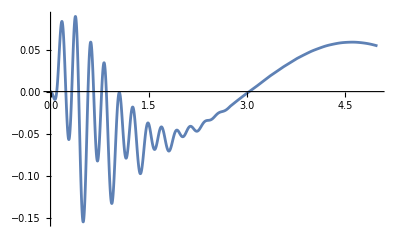

```mathematica
op=KroneckerProduct[SparseArray[{1,2}->1,3],IdentityMatrix[3]]+KroneckerProduct[SparseArray[{2,1}->1,3],IdentityMatrix[3]];
expval=TensorContract[h.op,{{2,3}}].rho/.sol;
Plot[expval,{t,0,5},PlotRange->All]
```

ADJOINT MASTER EQUATION
Set the initial conditions for the adjoint master equation

```mathematica
ainconds=Table[Subscript[q, ii][0]==Tr[h[[ii]].ρ0],{ii,1,81}];
```

Join the differential equations with the initial conditions for the master equation, solve the resulting system, compute the expected value of the operator op, and superimpose the master equation plot (light blue, thick line) onto the adjoint master equation plot (dark blue, thin line).

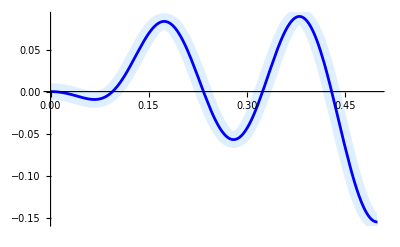

```mathematica
adeqs=Join[aleqs,ainconds]/.conds;
asol=NDSolve[adeqs,Normal[vq],{t,0,10.0}];
aexpval=TensorContract[h.op,{{2,3}}].vq/.asol;
Plot[{expval,aexpval},{t,0,.5},PlotRange->All,PlotStyle->{{LightBlue,Thickness[0.03]},{Blue,Thickness[0.005]}}]
```

Both plots yield exactly the same result.

## MasterEquation

MasterEquation[h, q, q0, transCE, transdd, transLi, nl, na, t] : h, q, q0 ∈ SparseArray, transCE, trasdd, transLi ∈ List;  na, nl ∈ Ingeters, t is a Mathematica symbol that represents the time variable
Returns a List of dimension  Length[h]=Length[q] that contains the Liouville differential equations that correspond to the Liouville superoperator including both the Hamiltonian and  Lindbladian parts generated using LiouvilleCommutator and LiouvilleLindbladian. MasterEquation is a wrapper of LiouvilleMasterEquation. h is the SparseArray that contains the matrix basis generated with MultiAtomBasis. The variable q should be a list of the density matrix coefficients, i.e., q = Tr[h ρ(t)] . The initial conditions are set through q0=ρ(0). The configuration variable  transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …} contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser ql_(k,1)and ql_(k,2), the Rabi parameter Rb_k, the detuning  Δ_k and the phase ϕ_k.  The configuration variable transdd={{tr_(1,1), tr_(1,2)}, α_1, β_1, Ω_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2, β_2, Ω_2 ,δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions corresponding to the two distinct α_k-th and β_k-th atoms (α_k≠ β_k). The strength of the interaction is given by Ω_k. δ_k is the detuning between these two transitions. For δ_k to be significant, it must be much smaller than both energy transitions themselves. Usually δ_k=0. transCE and transdd might be empty lists in case there are no light-matter interactions or/and there are no dipole-dipole interactions. The configuration variable transLi = {{tr_(1,1), tr_(1,2)}, α_1,  β_1,  γ_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2,  β_2, γ_2 , δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions ql_(k,1,1)→ ql_(k,1,2) (between the quantum levels tagged as ql_(k,1,1) and ql_(k,1,2)) and ql_(k,2,1)→ ql_(k,2,2) (between the quantum levels tagged as ql_(k,2,1) and ql_(k,2,2)) of the two distinct α_k-th and β_k-th atoms. The strength of the interaction is given by γ_k. δ_k is the detuning between these two transitions. These usually vanish, i.e. δ_k=0.

"Content"

#### Examples

Generate the differential equations for the density matrix coefficients that arise from a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE configuration variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

Assuming that the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩ have different energy differences and, therefore, do not interact among themselves, the transdd parameter is given by

```mathematica
transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{2,3}, {2,3},1,2,Subscript[Ω, 2],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0},{{2,3}, {2,3},2,1,Subscript[Ω, 2],0}};
```

The only  transitions with non-vanishing dipole matrix elements are  |1⟩ →|2⟩ and |2⟩ →|3⟩. The transition  |1⟩ →|2⟩ is tagged with the number 1, and the transition  |2⟩ →|3⟩ is tagged with the number 2. The strength of the dipole couplings are tagged accordingly: γ_1 is the coupling due to the dipole element of the transition 1 if only one atom is involved, γ_(1,1) is the coupling due to the dipole element of the transition 1 if two different atoms are involved,  γ_2 is the coupling due to the dipole element of the transition 2 if only one atom is involved and γ_(2,2) is the coupling due to the dipole element of the transition 2 if two different atoms are involved. The transLi configuration variable is thus given by

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0},{{1,2},{1,2},2,2,Subscript[γ, 1],0},{{1,2},{1,2},1,2,Subscript[γ, 1,1],0},{{1,2},{1,2},2,1,Subscript[γ, 1,1],0},{{2,3},{2,3},1,1,Subscript[γ, 2],0},{{2,3},{2,3},2,2,Subscript[γ, 2],0},{{1,2},{1,2},1,2,Subscript[γ, 2,2],0},{{1,2},{1,2},2,1,Subscript[γ, 2,2],0}};
```

```mathematica
nl= 3;
na =2;
rho=SparseArray[Table[{ii}->Subscript[ρ, ii][t],{ii,nl^(2na)}]]
h = MultiAtomBasis[nl,na]
```

SparseArray[…]

SparseArray[…]

Generate the differential equations corresponding to the master equation

```mathematica
eqs=MasterEquation[h,rho,transCE,transdd,transLi,nl,na,t];
```

Show the first 3 differential equations

```mathematica
eqs[[1;;3]]
```

MasterEquation[SparseArray[…],SparseArray[…],{{{1,2},1,R_1,Δ_1,0},{{1,2},2,R_1,Δ_1,0},{{2,3},1,R_2,Δ_2,ϕ},{{2,3},2,R_2,Δ_2,ϕ}}]

## AdjointMasterEquation

AdjointMasterEquation[h, q, q0, transCE, transdd, transLi, nl, na, t] : h, q, q0 ∈ SparseArray, transCE, trasdd, transLi ∈ List;  na, nl ∈ Ingeters, t is a Mathematica symbol that represents the time variable
Returns a List of dimension Length[h]=Length[q] that contains the Liouville differential equations that correspond to the adjoint Liouville superoperator including both the Hamiltonian and  Lindbladian parts generated using LiouvilleCommutator and LiouvilleLindbladianDagger. AdjointMasterEquation is a wrapper of LiouvilleAdjointMasterEquation. h is the SparseArray that contains the matrix basis generated with MultiAtomBasis. The variable q should be a list of the density matrix coefficients, i.e., q = Tr[h ρ(t)]. In the case of the adjoint master equation, these coefficients can be interpreted as the basis matrices in the Heisenberg picture. The initial conditions are set through q0=ρ(0). The configuration variable  transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …} contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser ql_(k,1)and ql_(k,2), the Rabi parameter Rb_k, the detuning  Δ_k and the phase ϕ_k.  The configuration variable transdd={{tr_(1,1), tr_(1,2)}, α_1, β_1, Ω_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2, β_2, Ω_2 ,δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions corresponding to the two distinct α_k-th and β_k-th atoms (α_k≠ β_k). The strength of the interaction is given by Ω_k. δ_k is the detuning between these two transitions. For δ_k to be significant, it must be much smaller than both energy transitions themselves. Usually δ_k=0. transCE and transdd might be empty lists in case there are no light-matter interactions or/and there are no dipole-dipole interactions. The configuration variable transLi = {{tr_(1,1), tr_(1,2)}, α_1,  β_1,  γ_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2,  β_2, γ_2 , δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions ql_(k,1,1)→ ql_(k,1,2) (between the quantum levels tagged as ql_(k,1,1) and ql_(k,1,2)) and ql_(k,2,1)→ ql_(k,2,2) (between the quantum levels tagged as ql_(k,2,1) and ql_(k,2,2)) of the two distinct α_k-th and β_k-th atoms. The strength of the interaction is given by γ_k. δ_k is the detuning between these two transitions. These usually vanish, i.e. δ_k=0.

"Content"

#### Example

Generate the differential equations of the Heisenberg picture basis matrices  that arise from a system consisting of two (na=2) three level (nl=3) atoms subject to two lasers with Rabi parameters R_1 and R_2 and detuning parameters Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with a Rabi parameter R_1 and the second couples |2⟩ and |3⟩ with a Rabi parameter R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. The transCE configuration variable that describes this light-matter interaction is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}};
```

Assuming that the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩ have different energy differences and, therefore, do not interact among themselves, the transdd parameter is given by

```mathematica
transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{2,3}, {2,3},1,2,Subscript[Ω, 2],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0},{{2,3}, {2,3},2,1,Subscript[Ω, 2],0}};
```

The only  transitions with non-vanishing dipole matrix elements are  |1⟩ →|2⟩ and |2⟩ →|3⟩. The transition  |1⟩ →|2⟩ is tagged with the number 1, and the transition  |2⟩ →|3⟩ is tagged with the number 2. The strength of the dipole couplings are tagged accordingly: γ_1 is the coupling due to the dipole element of the transition 1 if only one atom is involved, γ_(1,1) is the coupling due to the dipole element of the transition 1 if two different atoms are involved,  γ_2 is the coupling due to the dipole element of the transition 2 if only one atom is involved and γ_(2,2) is the coupling due to the dipole element of the transition 2 if two different atoms are involved. The transLi configuration variable is thus given by

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0},{{1,2},{1,2},2,2,Subscript[γ, 1],0},{{1,2},{1,2},1,2,Subscript[γ, 1,1],0},{{1,2},{1,2},2,1,Subscript[γ, 1,1],0},{{2,3},{2,3},1,1,Subscript[γ, 2],0},{{2,3},{2,3},2,2,Subscript[γ, 2],0},{{1,2},{1,2},1,2,Subscript[γ, 2,2],0},{{1,2},{1,2},2,1,Subscript[γ, 2,2],0}};
```

```mathematica
nl= 3;
na =2;
Q=SparseArray[Table[{ii}->Subscript[q, ii][t],{ii,nl^(2na)}]]
h = MultiAtomBasis[nl,na]
```

SparseArray[…]

SparseArray[…]

Generate the differential equations corresponding to the master equation

```mathematica
eqs=AdjointMasterEquation[h,Q,transCE,transdd,transLi,nl,na,t];
```

Show the first 3 differential equations

```mathematica
eqs[[1;;3]]
```

AdjointMasterEquation[SparseArray[…],SparseArray[…],{{{1,2},1,R_1,Δ_1,0},{{1,2},2,R_1,Δ_1,0},{{2,3},1,R_2,Δ_2,ϕ},{{2,3},2,R_2,Δ_2,ϕ}}]

## CleanUp

CleanUp[Op] : Op ∈ SparseArray
Returns a SparseArray of dimension Length[Op] with a cleaner set of ArrayRules. For example, in some cases it might eliminate vanishing imaginary elements.

"Content"

#### Example

Clean up the superoperator of the commutator of previous examples. Note that the raw SparseArray LiouvilleH contains 752 specified elements

```mathematica
LiouvilleH
```

SparseArray[…]

However, when it is cleaned up, it might have less specified elements

```mathematica
CleanUp[LiouvilleH]
```

SparseArray[…]

In this case, the SparseArray contains 704 specified elements, 48 less than the raw SparseArray.

The same thing happens with other superoperators obtained in previous examples

```mathematica
LiouvilleL
```

SparseArray[…]

```mathematica
CleanUp[LiouvilleL]
```

SparseArray[…]

```mathematica
LiouvilleLD
```

SparseArray[…]

```mathematica
CleanUp[LiouvilleLD]
```

SparseArray[…]

## FilteredClebschGordan

FilteredClebschGordan[{j_1, m_1}, {j_2, m_2}, {j, m}] :j_1, m_1, j_2, m_2, j, m ∈ Integers
Returns the Clebsch-Gordan coefficients ⟨j_1, m_1; j_2, m_2 | j, m ⟩ as given by GlebschGordan[{j1, m1}, {j2, m2}, {j, m}], provided that the triangular condition |j_1- j_2| ≤ j ≤ j_1+ j_2, and the magnetic quantum number condition m_1+ m_2= m are satisfied. Otherwise, it returns zero.

"Content"

#### Example

If j_1 = 2, m_1= 1, j_2 = 3, m_2 = 2, j = 4 and m=3 and, then the triangular and the magnetic quantum number conditions are met, and the function returns the  Clebsch-Gordan coefficient

```mathematica
FilteredClebschGordan[{2, 1}, {3, 2}, {4,3}]
```

-1/(2 √5)

However, if  j_1 = 2, m_1= 1, j_2 = 3, m_2 = 2,  j = 6 and m = 3, these conditions are not satisfied, and the function returns zero.

```mathematica
FilteredClebschGordan[{2, 1}, {3, 2}, {6,3}]
```

0

## DipoleMatrixElement

DipoleMatrixElement[i, jp, j, fp, f, mfp, mf ] i, jp, j, fp, f, mfp, mf ∈ Integers
Returns the angular part of dipole matrix element ⟨i, jp, fp, mfp| p | i, j, f, mf ⟩ leaving out the reduced matrix element. This separation follows the Wigner–Eckart theorem, in which a matrix element is expressed as the product of a reduced matrix element (independent of magnetic quantum numbers) and a Clebsch–Gordan coefficient or 3j-symbol that carries the angular dependence. i and j are the nuclear and electronic angular momentum quantum numbers, respectively, while f and mf denote the hyperfine total angular momentum and its magnetic quantum number, respectively.

"Content"

#### Example

The angular part of the dipole matrix element of an atom with nuclear angular momentum I=3/2 of the states N S^(1/2) F=2, M_F=0 and N P^(3/2)F=3 M_F=1 is given by

```mathematica
DipoleMatrixElement[3/2,3/2, 1/2, 3, 2, 1, 0 ]
```

{-1/(√10),ⅈ/(√10),0}

## InitialConditions

InitialConditions[h, q, q0, t] : h, q, q0 ∈ SparseArray
Returns a List of dimension Length[h]=Length[q] with the initial conditions for the density matrix coefficients of the form {q_1[0]==Tr[h_1.q0], q_2[0]==Tr[h_2.q0], ...}.  h is the SparseArray that contains the matrix basis generated with MultiAtomBasis. The variable q should be a list of the density matrix coefficients, i.e., q = Tr[h ρ(t)] . The initial conditions are stored in a SparseArray  q0=ρ(0) of dimensions √Length[q]×√Length[q]=√Length[h]×√Length[h].

"Content"

#### Example

Obtain the initial conditions corresponding to the initial density matrix

```mathematica
ρ0={{1/2,0,0,0},{0,1/2,0,0},{0,0,0,ⅈ },{0,0,-ⅈ,0}}
```

{{1/2,0,0,0},{0,1/2,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}}

Now we create the SparseArray that contains the coefficients of the density matrix as a function of time and a suitable matrix basis

```mathematica
rho=SparseArray[Table[{ii}->Subscript[ρ, ii][t],{ii,1,16}]]
h=MultiAtomBasis[2,2]
```

SparseArray[…]

SparseArray[…]

```mathematica
incon=InitialConditions[h,rho,ρ0,t]
```

{ρ_1[0]==1/2,ρ_2[0]==1/2,ρ_3[0]==0,ρ_4[0]==0,ρ_5[0]==0,ρ_6[0]==0,ρ_7[0]==0,ρ_8[0]==-√2,ρ_9[0]==0,ρ_10[0]==0,ρ_11[0]==0,ρ_12[0]==0,ρ_13[0]==0,ρ_14[0]==0,ρ_15[0]==0,ρ_16[0]==0}

It is important to note that, even if the initial density matrix stays the same, the initial conditions change if the matrix basis is different

```mathematica
h=MultiAtomBasis[4,1]
```

SparseArray[…]

```mathematica
incon=InitialConditions[h,rho,ρ0,t]
```

{ρ_1[0]==1/2,ρ_2[0]==1/2,ρ_3[0]==0,ρ_4[0]==0,ρ_5[0]==0,ρ_6[0]==0,ρ_7[0]==0,ρ_8[0]==0,ρ_9[0]==0,ρ_10[0]==0,ρ_11[0]==0,ρ_12[0]==0,ρ_13[0]==0,ρ_14[0]==0,ρ_15[0]==0,ρ_16[0]==-√2}

## LiouvilleLindbladianFromLindbladOperators

LiouvilleLindbladianFromLindbladOperators[h, liops, gammas]: h, liops, gammas ∈ SparseArray
Returns a SparseArray of dimension Length[h]×Length[h] containing the Liouville superopertor of the Lindbladian L = -1/2∑_(i,j)γ_(i,j)({A_i^†A_j, ρ}-2 A_jρ A_i^†). h is the matrix basis, liops contains the Lindblad operators {A_1, A_2, ..., A_m} and gammas contains the γ_(i,j) coefficients.

"Content"

#### Example

Build the Lindbladian superoperator of a 3 level system composed of the Lindblad operators A_1 = (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) and A_2 = (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0)  that correspond to the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩, respectively. The matrix basis that spans the 3 level space is

```mathematica
nl= 3;
na =1;
h = MultiAtomBasis[nl,na]
```

SparseArray[…]

The variable liops contains A_1and A_2in the SparseArray

```mathematica
liops = SparseArray[{{1,1,2}->1,{2,2,3}->1},{2,3,3}]
```

SparseArray[…]

The  γ_(i,j) coefficients are contained in the SparseArray

```mathematica
gammas = SparseArray[{{1,1}->Subscript[γ, 1],{2,2}->Subscript[γ, 2]},{2,2}]
```

SparseArray[…]

The Liouville superoperator is given by

```mathematica
Li = LiouvilleLindbladianFromLindbladOperators[h,liops,gammas]
```

SparseArray[…]

## LiouvilleDaggerLindbladianFromLindbladOperators

LiouvilleDaggerLindbladianFromLindbladOperators[h, liops, gammas]: h, liops, gammas ∈ SparseArray
Returns a SparseArray of dimension Length[h]×Length[h] containing the adjoint Liouville superopertor of the Lindbladian L^† = -1/2∑_(i,j)γ_(i,j)({A_i^†A_j, ρ}-2 A_i^†ρ A_j). Here h is the matrix basis, liops contains the Lindblad operators {A_1, A_2, ..., A_m} and gammas contains the γ_(i,j) coefficients.

"Content"

#### Example

Build the adjoint Lindbladian superoperator of a 3 level system composed of the Lindblad operators A_1 = (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) and A_2 = (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0)  that correspond to the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩, respectively. The matrix basis that spans the 3 level space is

```mathematica
nl= 3;
na =1;
h = MultiAtomBasis[nl,na]
```

SparseArray[…]

The variable liops contains A_1and A_2in the SparseArray

```mathematica
liops = SparseArray[{{1,1,2}->1,{2,2,3}->1},{2,3,3}]
```

SparseArray[…]

The  γ_(i,j) coefficients are contained in the SparseArray

```mathematica
gammas = SparseArray[{{1,1}->Subscript[γ, 1],{2,2}->Subscript[γ, 2]},{2,2}]
```

SparseArray[…]

The Liouville superoperator is given by

```mathematica
Lit = LiouvilleDaggerLindbladianFromLindbladOperators[h,liops,gammas]
```

SparseArray[…]

We verify that the adjoint Liouville operator is the conjugate transpose of the Liouville operator

```mathematica
Simplify[Normal[Conjugate[Transpose[Li]]-Lit],Assumptions->{Subscript[γ, 1]∈Reals, Subscript[γ, 2]∈Reals}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## TransitionLists

TransitionLists[i, Jlist, Flist, mFlist, levtrlist, laserlist, na, Λ, δ, ϕ, γ, W, M] : i, na ∈ Integers, Jlist, Flist, mFlist ∈ Lists of Integers, laserlist ∈ Lists, Λ, δ, ϕ, γ, W, M ∈ Symbols
TransitionLists[i, Jlist, Flist, mFlist, levtrlist, laserlist, na, Λ, Δϵ, δ, ϕ, γ, W, M] : i, na ∈ Integers, Jlist, Flist, mFlist ∈ Lists of Integers, laserlist ∈ Lists, Λ, Δϵ, δ, ϕ, γ, W, M ∈ Symbols
Returns the configuration lists necessary to build the master equations for alkali-metal atoms. i is the Integer nuclear angular momentum quantum number of the na atoms in the system. Jlist = {j_1, j_2, ..., j_n} is a List of the electronic angular momentum quantum numbers for the n orbitals considered in the model. Flist = {f_1, f_2, ..., f_n} is a List of  the hyperfine total angular momentums of the orbitals considered in the model. mFlist = {{m_(1,1), m_(1,2), ...}, {m_(2,1), m_(2,2), ... }, ..., {m_(n,1), m_(n,2), ... } } is a List of Lists, each containing the magnetic quantum numbers to be included in each of the orbitals.  Where, following the usual restrictions for the magnetic quantum numbers,  -F_k ≤ m_(k,1), m_(k,2), .... ≤ F_k. Thus, at most {m_(k,1), m_(k,2), ....} = Range[-F_k,F_k]. The configuration variable levtrlist  = {{q_1, q_2}, ...} is a list containing the transitions where q_1, q_2, ... index the groups of quantum levels characterized by the quantum numbers {j_1, f_1}, {j_2, f_2), ... , respectively. The configuration variable for the coherent sources interacting with the atom is the two-level nested list laserlist. The innermost list {{q_1, q_2} , e } has two elements. The first one is of the form {q_1, q_2} where  q_1 and q_2 index the two groups of quantum levels coupled by the coherent source. The second element e = {e_H, e_V, e_z} is the polarization unit vector of the source. TransitionLists only includes Rabi terms for those transitions that have non-vanishing contributions. The configuration Lists output are: levels, transitions, transdd, transLi, transCE. levels is a three-level nested list that primarily contains information about the orbitals’ quantum numbers. The innermost list is of the form {n_1, m_1, j_1, f_1} where n_1 indexes the orbital and m_1, j_1 and f_1 are the corresponding quantum numbers. The next level of the list groups together levels with the same j_1and f_1. Finally, the outermost list collects all these groups. transitions is a two-level nested list containing detailed information about the available transitions. The innermost list is of the form {q, {n_1, n_2}, Δm, ⟨p⟩} where q indexes the group of transitions, n_1 and n_2 are the orbitals’ tags, Δm is the change in the magnetic quantum number and ⟨p⟩ represents the angular part of the dipole moment matrix element. transdd and transCE are the configuration variables needed by Ham and HamDressed. transLi is the configuration variable needed by LiouvilleLindbladian. The variable transdd = {{tr_(1,1), tr_(1,2)}, α_1, β_1, Ω_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2, β_2, Ω_2, δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions corresponding to the two distinct α_k-th and β_k-th atoms (α_k≠ β_k). The strength of the interaction is given by Ω_k. δ_k is the detuning between these two transitions. For δ_k to be significant, it must be much smaller than both energy transitions themselves. Although typically δ_k=0, if Δϵ is provided as an argument of TransitionLists, it yields δ_k = Δϵ_1+ Δϵ_2+ ... where Δϵ_1,  Δϵ_2, .... are the energy shifts due to the Zeeman splitting, for example. If Δϵ is not provided as an argument of TransitionLists, it yields δ_k = 0.  The configuration variable transLi = {{tr_(1,1), tr_(1,2)}, α_1,  β_1,  γ_1 , δ_1}, {tr_(2,1), tr_(2,2)}, α_2,  β_2, γ_2 , δ_2}, …} contains the parameters for the dipole-dipole interaction.  tr_(k,1)={ql_(k,1,1), ql_(k,1,2)}, tr_(k,1)={ql_(k,2,1), ql_(k,2,2)} are the two interacting dipole transitions ql_(k,1,1)→ ql_(k,1,2) (between the quantum levels tagged as ql_(k,1,1) and ql_(k,1,2)) and ql_(k,2,1)→ ql_(k,2,2) (between the quantum levels tagged as ql_(k,2,1) and ql_(k,2,2)) of the two distinct α_k-th and β_k-th atoms. transCE = {{{ql_(1,1), ql_(1,2)}, α_1, Rb_1, Δ_1, ϕ_1}, {{ql_(2,1), ql_(2,2)},  α_2, Rb_2, Δ_2, ϕ_2}, …} contains the parameters for the light-matter interaction of the α_k-th atom. These parameters are: the two quantum levels excited by the laser ql_(k,1)and ql_(k,2), the Rabi parameter Rb_k, the detuning  Δ_k and the phase ϕ_k. Λ, Δϵ, δ and ϕ are the Symbols used as Rabi parameters, energy shifts and, detuning and phase,  respectively. γ, W, M are the Symbols used as the dipole-dipole couplings.

"Content"

#### Example

Generate the configuration variables for two ^87 Rb atoms taking in to account the orbitals 5 S_(1/2)F=2, 5 P_(3/2)F=3 and 5 D_(3/2)F=3. The TransitionLists configuration variables are

```mathematica
na=2;
Jlist = {1/2,3/2,3/2};
Flist={2,3,3};
mFlist={Range[-2,2],Range[-3,3], Range[-3,3]};
levtrlist={{1,2},{2,3}};
lasertrlist={{{1,2},{1/(√2),-ⅈ/(√2),0}},{{2,3},{1/(√2),ⅈ/(√2),0}}};
```

Notice that we have included all the possible values of the magnetic quantum number m for each one of the orbitals.

```mathematica
{levels, transitions, transdd, transLi, transCE}=TransitionLists[3/2,Jlist,Flist,mFlist,levtrlist,lasertrlist,na, R, Δϵ, δ,ϕ, γ, F, G];
```

As can be seen from the variable levels, there is a total of 19 quantum levels, given by (2F_1+1) + (2F_2+1) + (2F_3+1) = 2(2)+1 + 2(3)+1+2(3)+1

```mathematica
levels
```

{{{1,-2,1/2,2},{2,-1,1/2,2},{3,0,1/2,2},{4,1,1/2,2},{5,2,1/2,2}},{{6,-3,3/2,3},{7,-2,3/2,3},{8,-1,3/2,3},{9,0,3/2,3},{10,1,3/2,3},{11,2,3/2,3},{12,3,3/2,3}},{{13,-3,3/2,3},{14,-2,3/2,3},{15,-1,3/2,3},{16,0,3/2,3},{17,1,3/2,3},{18,2,3/2,3},{19,3,3/2,3}}}

In this case there are three groups of orbitals. These are indexed as follows:
1, characterized by the quantum numbers j_1=1/2 and f_1=2.
2, characterized by the quantum numbers j_2=3/2 and  f_2=3
3, characterized by the quantum numbers j_3=3/2 and f_3=3.
Each one of them is composed of the orbitals specified in the variable levels. The orbitals in group 1 are

```mathematica
levels[[1]]
```

{{1,-2,1/2,2},{2,-1,1/2,2},{3,0,1/2,2},{4,1,1/2,2},{5,2,1/2,2}}

the orbitals in group 2 are

```mathematica
levels[[2]]
```

{{6,-3,3/2,3},{7,-2,3/2,3},{8,-1,3/2,3},{9,0,3/2,3},{10,1,3/2,3},{11,2,3/2,3},{12,3,3/2,3}}

and the orbitals in group 3 are

```mathematica
levels[[3]]
```

{{13,-3,3/2,3},{14,-2,3/2,3},{15,-1,3/2,3},{16,0,3/2,3},{17,1,3/2,3},{18,2,3/2,3},{19,3,3/2,3}}

In the variable transistions the first number in the innermost list indexes the transition as stated by levtrlist. In this way the transition index 1 corresponds to any transition going from the levels of 5 S_(1/2)F=2, with j_1=1/2 and f=2 to those of 5 P_(3/2)F=3 with j_1=3/2 and f=3 as it is shown for the first 5 elements of transitions

```mathematica
transitions[[1;;5]]
```

{{1,{1,6},-1,{1/2,ⅈ/2,0}},{1,{1,7},0,{0,0,1/(√6)}},{1,{1,8},1,{-1/(2 √15),ⅈ/(2 √15),0}},{1,{2,7},-1,{1/(√6),ⅈ/(√6),0}},{1,{2,8},0,{0,0,2/(√15)}}}

Similarly, the transition index 2 corresponds to any transition going from the levels of 5 P_(3/2)F=3 with j_1=3/2 and f=3 to those of 5 D_(3/2)F=3 with j_1=3/2 and f=3 as it is shown below

```mathematica
transitions[[15;;19]]
```

{{1,{5,12},1,{-1/2,ⅈ/2,0}},{2,{6,13},0,{0,0,-(√(3/5))/2}},{2,{6,14},1,{1/(2 √10),-ⅈ/(2 √10),0}},{2,{7,13},-1,{1/(2 √10),ⅈ/(2 √10),0}},{2,{7,14},0,{0,0,-1/(√15)}}}

Notice the consistency between Δm and ⟨p⟩ in the previous lists. The first to elements of the innermost list of transdd are the coupled transitions. Consider terms 1 and 3 of transdd

```mathematica
transdd[[{1,3}]]
```

{{{1,6},{1,6},1,2,(G_1 γ_1)/2,0},{{1,6},{2,7},1,2,(G_3 γ_1)/(√6),Δϵ_1-Δϵ_2-Δϵ_6+Δϵ_7}}

The next two elements are the atomic indices. transdd  considers only couplings between different atoms, in this case atoms 1 and 2. The fifth element is the coupling strength which carries the transition and atomic indices. The last element is the detuning between the two transitions. Note that when the two coupled transitions are the same, the detuning vanishes, i.e. δ_1  = 0. Conversely, when the transitions are different, the detuning is nonzero, i.e. δ_3 = Δϵ_1-Δϵ_2-Δϵ_6+Δϵ_7. In this case, the energy shifts Δϵ_1, Δϵ_2, Δϵ_6, Δϵ_7 correspond to the quantum levels involved in the transitions. The variable transLi has a similar structure, however it can also couple transitions from the same atoms

```mathematica
transLi[[1;;5]]
```

{{{1,6},{1,6},1,1,γ_1/2,0},{{1,6},{1,6},1,2,(F_2 γ_1)/2,0},{{1,6},{1,6},2,1,(F_3 γ_1)/2,0},{{1,6},{1,6},2,2,γ_1/2,0},{{1,6},{2,7},1,1,γ_1/(√6),Δϵ_1-Δϵ_2-Δϵ_6+Δϵ_7}}

The configuration variable transCE contains only those transitions that have nonzero projections of the dipole moment matrix element on the polarization vector of the coherent source

```mathematica
transCE
```

{{{1,8},1,-R_1/(√30),δ_1-Δϵ_1+Δϵ_8,ϕ_(1,1)},{{1,8},2,-R_1/(√30),δ_1-Δϵ_1+Δϵ_8,ϕ_(1,2)},{{2,9},1,-R_1/(√10),δ_1-Δϵ_2+Δϵ_9,ϕ_(1,1)},{{2,9},2,-R_1/(√10),δ_1-Δϵ_2+Δϵ_9,ϕ_(1,2)},{{3,10},1,-R_1/(√5),δ_1-Δϵ_3+Δϵ_10,ϕ_(1,1)},{{3,10},2,-R_1/(√5),δ_1-Δϵ_3+Δϵ_10,ϕ_(1,2)},{{4,11},1,-R_1/(√3),δ_1-Δϵ_4+Δϵ_11,ϕ_(1,1)},{{4,11},2,-R_1/(√3),δ_1-Δϵ_4+Δϵ_11,ϕ_(1,2)},{{5,12},1,-R_1/(√2),δ_1-Δϵ_5+Δϵ_12,ϕ_(1,1)},{{5,12},2,-R_1/(√2),δ_1-Δϵ_5+Δϵ_12,ϕ_(1,2)},{{7,13},1,R_2/(2 √5),δ_2-Δϵ_7+Δϵ_13,ϕ_(2,1)},{{7,13},2,R_2/(2 √5),δ_2-Δϵ_7+Δϵ_13,ϕ_(2,2)},{{8,14},1,R_2/(2 √3),δ_2-Δϵ_8+Δϵ_14,ϕ_(2,1)},{{8,14},2,R_2/(2 √3),δ_2-Δϵ_8+Δϵ_14,ϕ_(2,2)},{{9,15},1,R_2/(√10),δ_2-Δϵ_9+Δϵ_15,ϕ_(2,1)},{{9,15},2,R_2/(√10),δ_2-Δϵ_9+Δϵ_15,ϕ_(2,2)},{{10,16},1,R_2/(√10),δ_2-Δϵ_10+Δϵ_16,ϕ_(2,1)},{{10,16},2,R_2/(√10),δ_2-Δϵ_10+Δϵ_16,ϕ_(2,2)},{{11,17},1,R_2/(2 √3),δ_2-Δϵ_11+Δϵ_17,ϕ_(2,1)},{{11,17},2,R_2/(2 √3),δ_2-Δϵ_11+Δϵ_17,ϕ_(2,2)},{{12,18},1,R_2/(2 √5),δ_2-Δϵ_12+Δϵ_18,ϕ_(2,1)},{{12,18},2,R_2/(2 √5),δ_2-Δϵ_12+Δϵ_18,ϕ_(2,2)}}

For example, consider the transition {1, 8}:

```mathematica
transitions[[3]]
```

{1,{1,8},1,{-1/(2 √15),ⅈ/(2 √15),0}}

This transition has dipole matrix element parallel to {1/√2, -ⅈ/√2 }, as specified in the first element of the laserlist configuration variable

```mathematica
lasertrlist[[1]]
```

{{1,2},{1/(√2),-ⅈ/(√2),0}}

Therefore, it is an element of transCE

```mathematica
transCE[[1]]
```

{{1,8},1,-R_1/(√30),δ_1-Δϵ_1+Δϵ_8,ϕ_(1,1)}

On the other hand, consider the transition {1,6}:

```mathematica
transitions[[1]]
```

{1,{1,6},-1,{1/2,ⅈ/2,0}}

This transition has dipole matrix element parallel to {1/√2, ⅈ/√2 }, which is orthogonal to  {1/√2, -ⅈ/√2 }. Hence, is not an element of transCE.

When Δϵ is not specified as an argument of TransitionLists the energy shifts are omitted from  transdd, transLi and transCE

```mathematica
{levels, transitions, transdd, transLi, transCE}=TransitionLists[3/2,Jlist,Flist,mFlist,levtrlist,lasertrlist,na, R, δ,ϕ, γ, F, G];
```

```mathematica
transdd[[{1,3}]]
```

{{{1,6},{1,6},1,2,(G_1 γ_1)/2,0},{{1,6},{2,7},1,2,(G_3 γ_1)/(√6),0}}

```mathematica
transLi[[1;;5]]
```

{{{1,6},{1,6},1,1,γ_1/2,0},{{1,6},{1,6},1,2,(F_2 γ_1)/2,0},{{1,6},{1,6},2,1,(F_3 γ_1)/2,0},{{1,6},{1,6},2,2,γ_1/2,0},{{1,6},{2,7},1,1,γ_1/(√6),0}}

```mathematica
transCE[[1;;6]]
```

{{{1,8},1,-R_1/(√30),δ_1,ϕ_(1,1)},{{1,8},2,-R_1/(√30),δ_1,ϕ_(1,2)},{{2,9},1,-R_1/(√10),δ_1,ϕ_(1,1)},{{2,9},2,-R_1/(√10),δ_1,ϕ_(1,2)},{{3,10},1,-R_1/(√5),δ_1,ϕ_(1,1)},{{3,10},2,-R_1/(√5),δ_1,ϕ_(1,2)}}

## FarField

FarField[transitions, levtrlist, countlist, atompos, nl, na, κ] : transitions, levtrlist, countlist, atompos ∈ Lists, nl, na ∈ Integers,  κ ∈ Symbols.
FarField[transitions, levtrlist, countlist, atompos, nl, na, κ, Δκ] : transitions, levtrlist, countlist, atompos ∈ Lists, nl, na ∈ Integers,  κ, Δκ ∈ Symbols.
Returns the far field operators a list of SparseArray objects of dimension Length[count-list] with the correlations of the far field given by E_l^†E_lwhere E_l = ∑_(α=1)^na ∑_n (p_n-(R̂)_α(R̂)_α·p_n)/R_α k_n^2 Exp[-ik_n(R_α-R)]σ_(n,α) is the far field operator in arbitrary units.  p_n is the dipole matrix element of the n-th transition, R_α=R-r_α= {X_α, Y_α, Z_α}  is the vector from the α-th atom located at r_α = {x_α, y_α , z_α} to the detector at position R = {X, Y , Z}. The magnitude of the transition’s wave vector is  k_n. The SparseArray object σ_(n,α) = |(n_1⟩)_(α α)⟨n_2| is the transition operator associated with the n-th transition between the n_1and n_2 orbitals of atom α as given by Sigma. The configuration variable transitions is a two-level nested list containing detailed information about the available transitions. The innermost list is of the form {q, {n_1, n_2}, Δm, ⟨p⟩} where q indexes the group of transitions, n_1 and n_2 are the orbitals’ tags, Δm is the change in the magnetic quantum number and ⟨p⟩ represents the angular part of the dipole moment matrix element. This variable might be obtained as part of the output of TransitionLists.  The configuration variable levtrlist  = {{q_1, q_2}, ...} is a list containing the transitions where q_1, q_2, ... index the groups of quantum levels characterized by the quantum numbers {j_1, f_1}, {j_2, f_2), ... , respectively. This is also a configuration variable for TransitionLists. The configuration variable countlist has the structure {{{q_1, q_2}, e, R }, ... } where q_1 and q_2 index the groups of quantum levels of the n-th transition, e = {e_1, e_2, e_3} is the polarization unit vector measured by the detector positioned at R = {X, Y , Z}. The Symbol κ is used to obtain the magnitude of the wave vector  k_nin the following way. If the Symbol Δκ is not provided as an argument of FarField, it is assumed  that the orbitals with the same quantum number f but different quantum number m are degenerate and therefore k_n=κ_n. If Δκ is provided as an argument of FarField, it is assumed that the degeneracy between the orbitals with different magnetic quantum  numbers m is lifted (for example, due to Zeeman splitting). In the latter case k_n=κ_n- Δκ_n_1+Δκ_n_2.

"Content"

#### Example

Generate the far-field operators of the two possible transitions of two ^87 Rb atoms, taking in to account the orbitals 5 S_(1/2)F=2, 5 P_(3/2)F=3 and 5 D_(3/2)F=3. We first obtain some of the configuration variables needed for FarField from TransitionLists

```mathematica
na=2;
Jlist = {1/2,3/2,3/2};
Flist={2,3,3};
mFlist={Range[-2,2],Range[-3,3], Range[-3,3]};
levtrlist={{1,2},{2,3}};
lasertrlist={{{1,2},{1/(√2),-ⅈ/(√2),0}},{{2,3},{1/(√2),ⅈ/(√2),0}}};
{levels, transitions, transdd, transLi, transCE}=TransitionLists[3/2,Jlist,Flist,mFlist,levtrlist,lasertrlist,na, R, Δϵ, δ,ϕ, γ, F, G];
```

In this case there are three groups of orbitals. These are indexed as follows:
1, characterized by the quantum numbers j_1=1/2 and f_1=2.
2, characterized by the quantum numbers j_2=3/2 and  f_2=3
3, characterized by the quantum numbers j_3=3/2 and f_3=3.
Each one of them is composed of the orbitals specified in the variable levels. The orbitals in group 1 are

```mathematica
levels[[1]]
```

{{1,-2,1/2,2},{2,-1,1/2,2},{3,0,1/2,2},{4,1,1/2,2},{5,2,1/2,2}}

the orbitals in group 2 are

```mathematica
levels[[2]]
```

{{6,-3,3/2,3},{7,-2,3/2,3},{8,-1,3/2,3},{9,0,3/2,3},{10,1,3/2,3},{11,2,3/2,3},{12,3,3/2,3}}

and the orbitals in group 3 are

```mathematica
levels[[3]]
```

{{13,-3,3/2,3},{14,-2,3/2,3},{15,-1,3/2,3},{16,0,3/2,3},{17,1,3/2,3},{18,2,3/2,3},{19,3,3/2,3}}

The orbitals in group 2 are

```mathematica
levels[[3]]
```

{{13,-3,3/2,3},{14,-2,3/2,3},{15,-1,3/2,3},{16,0,3/2,3},{17,1,3/2,3},{18,2,3/2,3},{19,3,3/2,3}}

We set the configuration countlist to generate two far-field operators. The first corresponds to transitions between orbitals in groups 1 and 2, with a dipole matrix element parallel to the polarization vector 1/√2{1, ⅈ, 0}. The second corresponds to transitions between orbitals in groups 2 and 3, with a dipole matrix element parallel to the polarization vector 1/√2{1, -ⅈ, 0}. Both detectors are placed at a distance R from the atomic system along the z-axis

```mathematica
countlist={{{1,2},{1/(√2),ⅈ/(√2),0},{0,0,R}},{{2,3},{1/(√2),-ⅈ/(√2),0},{0,0,R}}};
```

```mathematica
atompos={{0,0,0},{r,0,0}};
```

We notice from the variable levels that the number of levels is 19

```mathematica
nl=levels[[-1,-1,1]]
```

19

Finally, we calculate the far-field operators

```mathematica
{ffield1,ffield2}=FarField[transitions, levtrlist, countlist, atompos, nl, na,κ]
```

{SparseArray[<761>, {361, 361}],SparseArray[<839>, {361, 361}]}

## WDipoleDipoleElement

WDipoleDipoleElement[p1, p2, rhat, ζ] : p1, p2, rhat ∈ Lists,  ζ ∈ Symbols.
Returns the imaginary part of the Green’s function that governs the propagation of the electromagnetic field. The dipole moment vectors are given by p1 = {p1x, p1y, p1z} and p2 = {p2x, p2y, p2z}. The unit vector rhat  = {x, y , z} points from atom α to atom β when α ≠ β, and reduces to rhat= {0, 0, 0} in case it couples an atom with itself. The parameter ζ = κ r_(α,β) where κ denotes the magnitude of the wave vector and r_(α,β) is the distance between atoms α and β.

"Content"

#### Example

Plot the imaginary part of the Green’s function as a function of the distance between atoms. First we define the dipole matrix elements considering that both belong to the same transition

```mathematica
p1={1/(√3),ⅈ/(√3),0};
p2={1/(√3),ⅈ/(√3),0};
```

Assuming that the coupling corresponds to two atoms along the y axis

```mathematica
rhat={0,1,0};
```

and that the wave lenght is 0.780 μm, the imaginary part of the Green’s function is

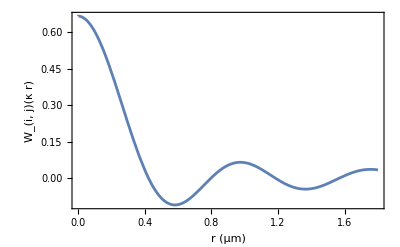

```mathematica
Plot[WDipoleDipoleElement[p1,p2,rhat, (2π)/0.780 r],{r,0,1.800},Axes->False,Frame->True,FrameLabel->{Style["r (μm)",20],Style["W_(i, j)(κ r)",20]},PlotRange->All]
```

## MDipoleDipoleElement

MDipoleDipoleElement[p1, p2, rhat, ζ] : p1, p2, rhat ∈ Lists,  ζ ∈ Symbols.
Returns the real part of the Green’s function that governs the propagation of the electromagnetic field. The dipole moment vectors are given by p1 = {p1x, p1y, p1z} and p2 = {p2x, p2y, p2z}. The unit vector rhat  = {x, y , z} points from atom α to atom β when α ≠ β, and reduces to rhat= {0, 0, 0} in case it couples an atom with itself. The parameter ζ = κ r_(α,β) where κ denotes the magnitude of the wave vector and r_(α,β) is the distance between atoms α and β.

"Content"

#### Example

Plot the real part of the Green’s function as a function of the distance between atoms. First we define the dipole matrix elements considering that both belong to the same transition

```mathematica
p1={1/(√3),ⅈ/(√3),0};
p2={1/(√3),ⅈ/(√3),0};
```

Assuming that the coupling corresponds to two atoms along the y axis

```mathematica
rhat={0,1,0};
```

and that the wave lenght is 0.780 μm, the imaginary part of the Green’s function is

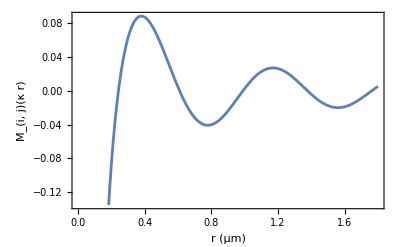

```mathematica
Plot[MDipoleDipoleElement[p1,p2,rhat, (2π)/0.780 r],{r,0,1.800},Axes->False,Frame->True,FrameLabel->{Style["r (μm)",20],Style["M_(i, j)(κ r)",20]}]
```

# Examples

These are some examples that walk users through the process of solving the dynamics of a variety of physical systems.

"Content"

## A single two-level atom

We set up the master equation for a single two-level atom. Using this solution, we plot the time dependence of the quantum-level populations. We also compute the emission as a function of the laser detuning.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

We start by setting the matrix basis. We set  the number of atoms (na) and the number of quantum levels (nl) per atom.  We then set the dimension of the Hilbert space (n) , define the basis (h) and create the time-dependent density matrix coefficients (ρ[t])

```mathematica
na=1;
nl=2;
n = nl^(2na);
h=MultiAtomBasis[nl,na]
rho=SparseArray[Table[ii->Subscript[ρ, ii][t],{ii,1,n}]]
```

SparseArray[…]

SparseArray[…]

Next, we set the parameters for the Hamiltonian. The transCE configuration variable, which describes this light–matter interaction, is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0}}
```

{{{1,2},1,R_1,Δ_1,0}}

This variable indicates that there is only one laser field, coupling the states |1⟩ and |2⟩ ({1,2}) of a single atom (1), with Rabi frequency R_1 and detuning Δ_1. The phase due to the atom’s position is taken to be zero, assuming the atom is located at the origin. Since there is only one atom, the variable transdd,which lists the coherent interactions between atoms is an empty list

```mathematica
transdd={}
```

{}

We can now compute the Hamiltonian

```mathematica
ham=Ham[transCE,transdd,nl,na,t];
MatrixForm[ham]
```

(0 | -ⅇ^(-ⅈ t Δ_1) R_1
-ⅇ^(ⅈ t Δ_1) R_1 | 0)

The Liouville operator corresponding to this Hamiltonian is

```mathematica
LiH=-LiouvilleCommutator[h,ham]
```

SparseArray[…]

We then set the Lindbladian parameters. These are defined via the configuration variable transLi

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0}}
```

{{{1,2},{1,2},1,1,γ_1,0}}

These parameters  mean that there is only one decay channel between the states |1⟩ and |2⟩ ({1,2}). This is a transition between the atom 1 and itself, therefore the two transition lists are followed by a 1,1. The parameter γ is the decay rate of the transition |1⟩ →  |2⟩. The final 0  in transLi represents the energy difference between the two transitions. In this case, both transitions are in fact the same, so the difference between the energy gaps is strictly zero. All together “{{1,2},{1,2},1,1,γ_1,0}” states that the decay involving  the state |1⟩ and |2⟩  ({1,2}) couples to itself ({1,2}), involves only one atom (1,1), has decay rate γ_1 and the energy gap difference between transitions is 0 as the transition is coupling to itself. For more complex systems, each transition may couple to many other transitions.

Having defined transLi, we are ready to compute the Liouville operator corresponding to the Lindbladian

```mathematica
LiL = LiouvilleLindbladian[h,transLi,nl,na]
```

SparseArray[…]

The overall Liouville operator is the sum of the Hamiltonian and Lindblad Liouville operators

```mathematica
Li =LiH+LiL
```

SparseArray[…]

At this point we are ready to generate the system of differential equations for the density matrix coefficients

```mathematica
eqs=LiouvilleMasterEquation[rho,Li,t]//ExpToTrig
```

{ρ_1'[t]==γ_1 ρ_2[t]+√2 Sin[t Δ_1] R_1 ρ_3[t]-√2 Cos[t Δ_1] R_1 ρ_4[t],ρ_2'[t]==-γ_1 ρ_2[t]-√2 Sin[t Δ_1] R_1 ρ_3[t]+√2 Cos[t Δ_1] R_1 ρ_4[t],ρ_3'[t]==-√2 Sin[t Δ_1] R_1 ρ_1[t]+√2 Sin[t Δ_1] R_1 ρ_2[t]-1/2 γ_1 ρ_3[t],ρ_4'[t]==√2 Cos[t Δ_1] R_1 ρ_1[t]-√2 Cos[t Δ_1] R_1 ρ_2[t]-1/2 γ_1 ρ_4[t]}

For a numerical example, we set the physical parameters to

```mathematica
parmvals={Subscript[R, 1]->12.0,Subscript[Δ, 1]->1.0,Subscript[γ, 1]->1.5}
eqsn=eqs/.parmvals
```

{R_1→12.,Δ_1→1.,γ_1→1.5}

{ρ_1'[t]==1.5 ρ_2[t]+16.9706 Sin[1. t] ρ_3[t]-16.9706 Cos[1. t] ρ_4[t],ρ_2'[t]==-1.5 ρ_2[t]-16.9706 Sin[1. t] ρ_3[t]+16.9706 Cos[1. t] ρ_4[t],ρ_3'[t]==-16.9706 Sin[1. t] ρ_1[t]+16.9706 Sin[1. t] ρ_2[t]-0.75 ρ_3[t],ρ_4'[t]==16.9706 Cos[1. t] ρ_1[t]-16.9706 Cos[1. t] ρ_2[t]-0.75 ρ_4[t]}

We can assume that the system is initially in the lowest energy level  |1⟩ . Therefore, we set the initial conditions, noting that rho0 is given as a matrix

```mathematica
rho0={{1,0},{0,0}};
incon=InitialConditions[h,rho,rho0,t]
```

{ρ_1[0]==1,ρ_2[0]==0,ρ_3[0]==0,ρ_4[0]==0}

The final ODE is obtained by joining the differential equations and the initial conditions

```mathematica
diffeq=Join[eqsn,incon]
```

{ρ_1'[t]==1.5 ρ_2[t]+16.9706 Sin[1. t] ρ_3[t]-16.9706 Cos[1. t] ρ_4[t],ρ_2'[t]==-1.5 ρ_2[t]-16.9706 Sin[1. t] ρ_3[t]+16.9706 Cos[1. t] ρ_4[t],ρ_3'[t]==-16.9706 Sin[1. t] ρ_1[t]+16.9706 Sin[1. t] ρ_2[t]-0.75 ρ_3[t],ρ_4'[t]==16.9706 Cos[1. t] ρ_1[t]-16.9706 Cos[1. t] ρ_2[t]-0.75 ρ_4[t],ρ_1[0]==1,ρ_2[0]==0,ρ_3[0]==0,ρ_4[0]==0}

We can finally obtain the solution of the ODE via

```mathematica
sol=NDSolve[diffeq,Normal[rho],{t,0,5}][[1]]
```

{ρ_1[t]→InterpolatingFunction[…][t],ρ_2[t]→InterpolatingFunction[…][t],ρ_3[t]→InterpolatingFunction[…][t],ρ_4[t]→InterpolatingFunction[…][t]}

Now we can observe the dynamics of different expectation values or the density matrix coefficients. For example, to compute the populations of |1⟩ and |2⟩ we calculate the expectation values

```mathematica
pop1=ExpectationValue[h,rho,{{1,0},{0,0}}]
pop2=ExpectationValue[h,rho,{{0,0},{0,1}}]
pop1n=pop1/.sol;
pop2n=pop2/.sol;
```

ρ_1[t]

ρ_2[t]

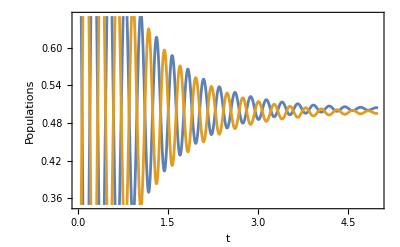

```mathematica
Plot[{pop1n,pop2n},{t,0,5},Axes->False,Frame->True,FrameLabel->{Style["t", 20],Style["Populations",20]}]
```

We can also perform a spectroscopic analysis of the emission of the two-level system by sweeping the detuning and evaluating the emission as the expectation value ⟨σ_(1,2)^†σ_(1,2)⟩ where σ_(1,2) = |1⟩⟨2|

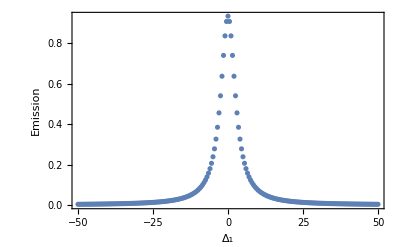

```mathematica
nd=200;
rho0={{1,0},{0,1}};
incon=InitialConditions[h,rho,rho0,t];
σ12=SparseArray[{{1,2}->1},2];
expval=ExpectationValue[h,rho,Transpose[σ12].σ12];
listplot={};
Do[
det=-50+100jj/nd;
parmvals={Subscript[R, 1]->2.0,Subscript[Δ, 1]->det,Subscript[γ, 1]->1.5};
eqsn=eqs/.parmvals;
diffeq=Join[eqsn,incon];
sol=NDSolve[diffeq,Normal[rho],{t,0,10}][[1]];
expvaln=expval/.sol/.{t->10};
AppendTo[listplot,{det,expvaln}];
,{jj,0,nd}]

ListPlot[listplot,Axes->False,Frame->True,FrameLabel->{Style["Δ_1",20],Style["Emission",20]},PlotRange->All]
```

It’s possible to shorten the process of obtaining the differential equations by using MasterEquation, which is a wrapper for LiouvilleMasterEquation, LiouvilleLindbladian, LiouvilleCommutator, and Ham

```mathematica
rho0=SparseArray[{{1,1}->1},2];
eqs=MasterEquation[h,rho,rho0,transCE,transdd,transLi,nl,na,t]
```

{ρ_1'[t]==γ_1 ρ_2[t]+√2 Sin[t Δ_1] R_1 ρ_3[t]-√2 Cos[t Δ_1] R_1 ρ_4[t],ρ_2'[t]==-γ_1 ρ_2[t]-√2 Sin[t Δ_1] R_1 ρ_3[t]+√2 Cos[t Δ_1] R_1 ρ_4[t],ρ_3'[t]==-√2 Sin[t Δ_1] R_1 ρ_1[t]+√2 Sin[t Δ_1] R_1 ρ_2[t]-1/2 γ_1 ρ_3[t],ρ_4'[t]==√2 Cos[t Δ_1] R_1 ρ_1[t]-√2 Cos[t Δ_1] R_1 ρ_2[t]-1/2 γ_1 ρ_4[t],ρ_1[0]==1,ρ_2[0]==0,ρ_3[0]==0,ρ_4[0]==0}

In simpler cases one may be able to obtain an analytical solution. For example, if the drive is turned off and the system is initially in the excited state |2⟩ , we readily obtain the typical equations for spontaneous emission

```mathematica
ode=Join[eqs/.{Subscript[R, 1]->0},Table[Subscript[ρ, ii][0]==KroneckerDelta[ii,2],{ii,n}]]
rhon=Normal[rho];
DSolve[ode,rhon,t]
```

{ρ_1'[t]==γ_1 ρ_2[t],ρ_2'[t]==-γ_1 ρ_2[t],ρ_3'[t]==-1/2 γ_1 ρ_3[t],ρ_4'[t]==-1/2 γ_1 ρ_4[t],ρ_1[0]==1,ρ_2[0]==0,ρ_3[0]==0,ρ_4[0]==0,ρ_1[0]==0,ρ_2[0]==1,ρ_3[0]==0,ρ_4[0]==0}

## Two two-level atoms

We set up the master equation for two two-level atoms. Using its solution, we plot the time dependence of the quantum-level populations. We also perform a spectroscopic analysis of the emission by sweeping the detuning and evaluating the correlation between the emissions of the two atoms.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

We start by setting the matrix basis. We set  the number of atoms (na) and the number of quantum levels (nl) per atom.  We then set the dimension of the Hilbert space (n) , define the basis (h) and create the time-dependent density matrix coefficients (ρ[t])

```mathematica
na=2;
nl=2;
n = nl^(2na);
h=MultiAtomBasis[nl,na]
rho=SparseArray[Table[ii->Subscript[ρ, ii][t],{ii,1,n}]]
```

SparseArray[…]

SparseArray[…]

Next, we set the parameters for the Hamiltonian. The transCE configuration variable, which describes this light–matter interaction, is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],ϕ}}
```

{{{1,2},1,R_1,Δ_1,0},{{1,2},2,R_1,Δ_1,ϕ}}

This variable indicates that there is only one laser coupling the states |1⟩ and |2⟩ ({1,2}) for both atoms (1 ) and (2), with Rabi parameter R_1 and detuning Δ_1. Note that a list of parameters per atom is necessary. The phase due to the atoms’ positions is taken to be zero for the first atom and ϕ for the second. Assuming that both atoms lie along the propagation direction of the incident field, there must be a phase difference of ϕ between them. The variable transdd, which lists the coherent interactions between atoms, is

```mathematica
transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0}}
```

{{{1,2},{1,2},1,2,Ω_1,0},{{1,2},{1,2},2,1,Ω_1,0}}

The first two elements are the transitions that couple to each other. The list {1,2} appears twice. Each transition couples to each transition with the same energy gap. The next two numbers indicate which two atoms are involved. Ω_1 indicates the strength of the coupling. 0 indicates the energy difference between the transitions. All together “{{1,2},{1,2},1,2,Ω_1,0}” means that the transition {1,2} in atom 1 is coupled to the transition {1,2} in atom 2, with strength Ω_1 and that there is no energy gap difference between the two transitions. The list is then repeated with the numbers indicating the atoms switched as the coupling is symmetrical under atomic exchanges.  In a more complex system, each atomic transition could be coupled to several other transitions and as such each coupling would have to be entered separately using the same format.

With these variables set, we compute the Hamiltonian

```mathematica
ham=Ham[transCE,transdd,nl,na,t];
MatrixForm[ham]
```

(0 | -ⅇ^(ⅈ (ϕ-t Δ_1)) R_1 | -ⅇ^(-ⅈ t Δ_1) R_1 | 0
-ⅇ^(ⅈ (-ϕ+t Δ_1)) R_1 | 0 | Ω_1 | -ⅇ^(-ⅈ t Δ_1) R_1
-ⅇ^(ⅈ t Δ_1) R_1 | Ω_1 | 0 | -ⅇ^(ⅈ (ϕ-t Δ_1)) R_1
0 | -ⅇ^(ⅈ t Δ_1) R_1 | -ⅇ^(ⅈ (-ϕ+t Δ_1)) R_1 | 0)

The Liouville operator corresponding to the Hamiltonian is given by

```mathematica
LiH=-LiouvilleCommutator[h,ham]
```

SparseArray[…]

We then set the Lindbladian parameters. These are entered through the configuration variable transLi

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0},{{1,2},{1,2},2,2,Subscript[γ, 1],0},{{1,2},{1,2},1,2,Subscript[γ, 1,2],0},{{1,2},{1,2},2,1,Subscript[γ, 1,2],0}}
```

{{{1,2},{1,2},1,1,γ_1,0},{{1,2},{1,2},2,2,γ_1,0},{{1,2},{1,2},1,2,γ_(1,2),0},{{1,2},{1,2},2,1,γ_(1,2),0}}

The first two entries of transLi list the decay channels between the states |1⟩ and |2⟩ ({1,2}) for each atom. These transitions occur internally within each atom, so the next two entries are repeated atomic indezes 1,1 and 2,2, meaning that the transition involves only that specific atom. The parameter γ_1corresponds to the decay rate of this transition. The last two terms give rise to the collective channels formed by the transitions |1⟩ →  |2⟩ between different atoms.  The parameter  γ_(1,2) is the collective decay rate of this transition. The final 0  in transLi represents the energy difference between the two transitions. In this case, both transitions are in fact the same, so the difference between the energy gaps is  zero. Note that the list {1,2} appears twice. This is because transitions with the same energy gap are coupled, meaning that any  transition must couple to itself. In more complex systems, however, there may be different transitions with the same or nearly identical energy gaps which are therefore coupled.

Having defined transLi, we are ready to compute the Liouville operator corresponding to the Lindbladian

```mathematica
LiL = LiouvilleLindbladian[h,transLi,nl,na]
```

SparseArray[…]

The overall Liouville operator is the sum of the Hamiltonian and Lindblad Liouville operators

```mathematica
Li =LiH+LiL
```

SparseArray[…]

At this point we are ready to generate the system of differential equations for the density matrix coefficients of the variable rho

```mathematica
eqs=LiouvilleMasterEquation[rho,Li,t]//ExpToTrig;
eqs[[1;;2]]
```

{ρ_1'[t]==γ_1 ρ_2[t]-√2 Sin[ϕ-t Δ_1] R_1 ρ_3[t]-√2 Cos[ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_5[t]+√2 Sin[t Δ_1] R_1 ρ_9[t]+γ_(1,2) ρ_11[t]-√2 Cos[t Δ_1] R_1 ρ_13[t]+γ_(1,2) ρ_16[t],ρ_2'[t]==-γ_1 ρ_2[t]+√2 Sin[ϕ-t Δ_1] R_1 ρ_3[t]+√2 Cos[ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_6[t]+√2 Sin[t Δ_1] R_1 ρ_10[t]-1/2 γ_(1,2) ρ_11[t]-Ω_1 ρ_12[t]-√2 Cos[t Δ_1] R_1 ρ_14[t]+Ω_1 ρ_15[t]-1/2 γ_(1,2) ρ_16[t]}

For a numerical example, we set the physical parameters to

```mathematica
parmvals={Subscript[R, 1]->12.0,Subscript[Δ, 1]->1.0,ϕ->1.1,Subscript[γ, 1]->1.5,Subscript[γ, 1,2]->0.5,Subscript[Ω, 1]->0.7}
eqsn=eqs/.parmvals;
eqsn[[1;;2]]
```

{R_1→12.,Δ_1→1.,ϕ→1.1,γ_1→1.5,γ_(1,2)→0.5,Ω_1→0.7}

{ρ_1'[t]==1.5 ρ_2[t]-16.9706 Sin[1.1-1. t] ρ_3[t]-16.9706 Cos[1.1-1. t] ρ_4[t]+1.5 ρ_5[t]+16.9706 Sin[1. t] ρ_9[t]+0.5 ρ_11[t]-16.9706 Cos[1. t] ρ_13[t]+0.5 ρ_16[t],ρ_2'[t]==-1.5 ρ_2[t]+16.9706 Sin[1.1-1. t] ρ_3[t]+16.9706 Cos[1.1-1. t] ρ_4[t]+1.5 ρ_6[t]+16.9706 Sin[1. t] ρ_10[t]-0.25 ρ_11[t]-0.7 ρ_12[t]-16.9706 Cos[1. t] ρ_14[t]+0.7 ρ_15[t]-0.25 ρ_16[t]}

We can assume that the atoms are both initially in the lowest energy level  |1⟩ . Therefore, we set the initial conditions to ρ_0=η_0⊗η_0 where η_0=|0⟩⟨0|

```mathematica
η0=SparseArray[{{1,1}->1},2]
rho0=KroneckerProduct[η0,η0]
incon=InitialConditions[h,rho,rho0,t]
```

SparseArray[…]

SparseArray[…]

{ρ_1[0]==1,ρ_2[0]==0,ρ_3[0]==0,ρ_4[0]==0,ρ_5[0]==0,ρ_6[0]==0,ρ_7[0]==0,ρ_8[0]==0,ρ_9[0]==0,ρ_10[0]==0,ρ_11[0]==0,ρ_12[0]==0,ρ_13[0]==0,ρ_14[0]==0,ρ_15[0]==0,ρ_16[0]==0}

The final ODE is obtained by joining the differential equations and the initial conditions

```mathematica
diffeq=Join[eqsn,incon];
diffeq[[{1,2,17,18}]]
```

{ρ_1'[t]==1.5 ρ_2[t]-16.9706 Sin[1.1-1. t] ρ_3[t]-16.9706 Cos[1.1-1. t] ρ_4[t]+1.5 ρ_5[t]+16.9706 Sin[1. t] ρ_9[t]+0.5 ρ_11[t]-16.9706 Cos[1. t] ρ_13[t]+0.5 ρ_16[t],ρ_2'[t]==-1.5 ρ_2[t]+16.9706 Sin[1.1-1. t] ρ_3[t]+16.9706 Cos[1.1-1. t] ρ_4[t]+1.5 ρ_6[t]+16.9706 Sin[1. t] ρ_10[t]-0.25 ρ_11[t]-0.7 ρ_12[t]-16.9706 Cos[1. t] ρ_14[t]+0.7 ρ_15[t]-0.25 ρ_16[t],ρ_1[0]==1,ρ_2[0]==0}

We can finally obtain the solution of the ODE as

```mathematica
sol=NDSolve[diffeq,Normal[rho],{t,0,5}][[1]];
sol[[1;;2]]
```

{ρ_1[t]→InterpolatingFunction[…][t],ρ_2[t]→InterpolatingFunction[…][t]}

Now we can observe the dynamics of different expectation values. For example, to compute the populations of levels |1⟩ and |2⟩ for both atoms we calculate the expectation values

```mathematica
p1=SparseArray[{{1,1}->1},2];
p2=SparseArray[{{2,2}->1},2];
one=SparseArray[{{1,1}->1,{2,2}->1},2];
pop11=ExpectationValue[h,rho,KroneckerProduct[p1,one]]
pop21=ExpectationValue[h,rho,KroneckerProduct[p2,one]]
pop12=ExpectationValue[h,rho,KroneckerProduct[one,p1]]
pop22=ExpectationValue[h,rho,KroneckerProduct[one,p2]]

pop11n=pop11/.sol;
pop21n=pop21/.sol;
pop12n=pop12/.sol;
pop22n=pop22/.sol;
```

ρ_1[t]+ρ_2[t]

ρ_5[t]+ρ_6[t]

ρ_1[t]+ρ_5[t]

ρ_2[t]+ρ_6[t]

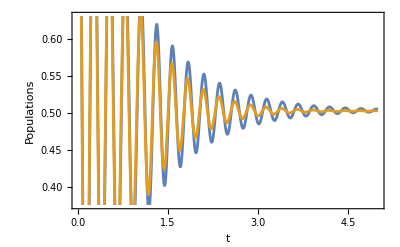

```mathematica
Plot[{pop11n,pop12n},{t,0,5},Axes->False,Frame->True,FrameLabel->{Style["t", 20],Style["Populations",20]}]
```

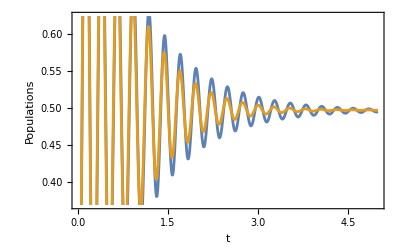

```mathematica
Plot[{pop21n,pop22n},{t,0,5},Axes->False,Frame->True,FrameLabel->{Style["t", 20],Style["Populations",20]}]
```

We can also perform a spectroscopic analysis of the emission of the two-level system by sweeping the detuning of the pump laser and evaluating the correlation function corr = ⟨σ_(2,1)^1σ_(1,2)^2+σ_(2,1)^2σ_(1,2)^1⟩ where σ_(1,2)^1 =1⊗ |1⟩⟨2| and σ_(1,2)^2 = |1⟩⟨2|⊗1

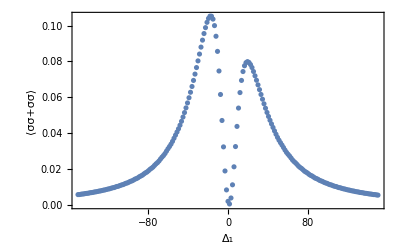

```mathematica
nd=200;
η0=SparseArray[{{1,1}->1},2];
rho0=KroneckerProduct[η0,η0];
incon=InitialConditions[h,rho,rho0,t];
corr=KroneckerProduct[SparseArray[{{1,2}->1},2],SparseArray[{{2,1}->1},2]]+KroneckerProduct[SparseArray[{{2,1}->1},2],SparseArray[{{1,2}->1},2]];
expval=ExpectationValue[h,rho,corr];
listplot={};
Do[
det=-150+300jj/nd;
parmvals={Subscript[R, 1]->12.0,Subscript[Δ, 1]->det,ϕ->1.1,Subscript[γ, 1]->1.5,Subscript[γ, 1,2]->0.5,Subscript[Ω, 1]->0.7};
eqsn=eqs/.parmvals;
diffeq=Join[eqsn,incon];
sol=NDSolve[diffeq,Normal[rho],{t,0,10}][[1]];
expvaln=expval/.sol/.{t->10};
AppendTo[listplot,{det,expvaln}];
,{jj,0,nd}]

ListPlot[listplot,Axes->False,Frame->True,FrameLabel->{Style["Δ_1",20],Style["⟨σσ+σσ⟩",20]},PlotRange->All]
```

It is possible to streamline the process of obtaining the differential equations by using MasterEquation, which is a wrapper for LiouvilleMasterEquation, LiouvilleLindbladian, LiouvilleCommutator, and Ham

```mathematica
η0=SparseArray[{{1,1}->1},2]
rho0=KroneckerProduct[η0,η0]
eqs=MasterEquation[h,rho,rho0,transCE,transdd,transLi,nl,na,t];
eqs[[{1,2,17,18}]]
```

SparseArray[…]

SparseArray[…]

{ρ_1'[t]==γ_1 ρ_2[t]-√2 Sin[ϕ-t Δ_1] R_1 ρ_3[t]-√2 Cos[ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_5[t]+√2 Sin[t Δ_1] R_1 ρ_9[t]+γ_(1,2) ρ_11[t]-√2 Cos[t Δ_1] R_1 ρ_13[t]+γ_(1,2) ρ_16[t],ρ_2'[t]==-γ_1 ρ_2[t]+√2 Sin[ϕ-t Δ_1] R_1 ρ_3[t]+√2 Cos[ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_6[t]+√2 Sin[t Δ_1] R_1 ρ_10[t]-1/2 γ_(1,2) ρ_11[t]-Ω_1 ρ_12[t]-√2 Cos[t Δ_1] R_1 ρ_14[t]+Ω_1 ρ_15[t]-1/2 γ_(1,2) ρ_16[t],ρ_1[0]==1,ρ_2[0]==0}

Note that in this case the initial condition was set using rho0 in sparse array form.

## Five two-level atoms

We set up the master equation for a chain of five two-level atoms coupled via nearest-neighbor interactions. Using the solution, we plot the time dependence of the correlations between the emissions of neighboring atoms and of the atoms at the edges of the chain. We also perform a spectroscopic analysis of the emission by sweeping the detuning and evaluating correlations.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

We start by setting the matrix basis. We set  the number of atoms (na) and the number of quantum levels (nl) per atom.  We then set the dimension of the Hilbert space (n) , define the basis (h) and create the time-dependent density matrix coefficients (ρ[t])

```mathematica
na=5;
nl=2;
n = nl^(2na);
h=MultiAtomBasis[nl,na]
rho=SparseArray[Table[ii->Subscript[ρ, ii][t],{ii,1,n}]]
```

SparseArray[<7776>, {1024, 32, 32}]

SparseArray[…]

Next, we set the Hamiltonian parameters. The transCE configuration variable, which describes this light–matter interaction, is

```mathematica
transCE=Table[{{1,2},ii, Subscript[R, 1], Subscript[Δ, 1],(ii-1)ϕ},{ii,1,5}]
```

{{{1,2},1,R_1,Δ_1,0},{{1,2},2,R_1,Δ_1,ϕ},{{1,2},3,R_1,Δ_1,2 ϕ},{{1,2},4,R_1,Δ_1,3 ϕ},{{1,2},5,R_1,Δ_1,4 ϕ}}

This variable indicates that there is only one laser coupling the states |1⟩ and |2⟩ ({1,2}) of the 5 atoms, with Rabi frequency R_1 and detuning Δ_1. The phase due to the atoms’ positions is taken to be zero for the first atom and increase by ϕ for each subsequent atom. Assuming that the 5 atoms lie along the propagation direction of the incident field, there must be a phase difference of ϕ between each consecutive pair of atoms. If the interaction only occurs between first neighbours the variable transdd, which lists the coherent interactions among atoms, is given by

```mathematica
transdd=Join[Table[{{1,2},{1,2},ii,ii+1,Subscript[Ω, 1],0},{ii,1,na-1}],Table[{{1,2},{1,2},ii+1,ii,Subscript[Ω, 1],0},{ii,1,na-1}]]
```

{{{1,2},{1,2},1,2,Ω_1,0},{{1,2},{1,2},2,3,Ω_1,0},{{1,2},{1,2},3,4,Ω_1,0},{{1,2},{1,2},4,5,Ω_1,0},{{1,2},{1,2},2,1,Ω_1,0},{{1,2},{1,2},3,2,Ω_1,0},{{1,2},{1,2},4,3,Ω_1,0},{{1,2},{1,2},5,4,Ω_1,0}}

The first two elements are the coupled transitions. The list {1,2} appears twice. This is because transitions with the same energy gap are coupled, meaning that any existing transition must couple to itself. In more complex systems, however, there may be different transitions with the same or nearly identical energy gaps that are therefore coupled.  The following two numbers (1,2) in the first element and (2,1) in the second element label the atoms. Ω_1 sets the coupling strength between these two transitions. The final 0  in each term represents the energy difference between the two coupled transitions. In this case, both transitions are in fact the same, so the difference between the energy gaps is strictly zero. In the case of two different transitions with similar energies, this number must be set equal to their energy difference. The lists are repeated with the atomic numbers switched as these interactions are symmetrical under exchange of atoms.

We compute the Hamiltonian

```mathematica
ham=Ham[transCE,transdd,nl,na,t]
```

SparseArray[…]

The Liouville operator corresponding to the Hamiltonian is given by (this calculation might take longer than the previous examples due to the number of elements)

```mathematica
LiH=-LiouvilleCommutator[h,ham]
```

SparseArray[<18496>, {1024, 1024}]

We then set the Lindbladian parameters. These are entered through the configuration variable transLi

```mathematica
transLi=Join[Table[{{1,2},{1,2},ii,ii,Subscript[γ, 1],0},{ii,na}],Table[{{1,2},{1,2},ii,ii+1,Subscript[γ, 1,2],0},{ii,na-1}],Table[{{1,2},{1,2},ii+1,ii,Subscript[γ, 1,2],0},{ii,na-1}]]
```

{{{1,2},{1,2},1,1,γ_1,0},{{1,2},{1,2},2,2,γ_1,0},{{1,2},{1,2},3,3,γ_1,0},{{1,2},{1,2},4,4,γ_1,0},{{1,2},{1,2},5,5,γ_1,0},{{1,2},{1,2},1,2,γ_(1,2),0},{{1,2},{1,2},2,3,γ_(1,2),0},{{1,2},{1,2},3,4,γ_(1,2),0},{{1,2},{1,2},4,5,γ_(1,2),0},{{1,2},{1,2},2,1,γ_(1,2),0},{{1,2},{1,2},3,2,γ_(1,2),0},{{1,2},{1,2},4,3,γ_(1,2),0},{{1,2},{1,2},5,4,γ_(1,2),0}}

The first five entries of transLi list the decay channels between the states |1⟩ and |2⟩ ({1,2}) for each atom. These transitions occur internally within each atom, so the next two transition entries are (1, 1), (2, 2), (3, 3), (4, 4) and (5, 5) respectively indicating that each term involves only that specific atom. The parameter γ_1corresponds to the decay rate of this transition. The last eight terms give rise to the collective channels formed between the transitions |1⟩ →  |2⟩ between neighbouring atoms.  The parameter  γ_(1,2) is collective decay rate of this kind of transition. The final 0  in each term transLi represents the energy difference between the two transitions. In this case, all these transitions are in fact the same, so the difference between the energy gaps is  zero.

Having defined transLi, we are ready to compute the Liouville operator corresponding to the Lindbladian (this might take longer than the previous examples due to the number of elements)

```mathematica
LiL = LiouvilleLindbladian[h,transLi,nl,na]
```

SparseArray[<8447>, {1024, 1024}]

The overall Liouville operator is the sum of the Hamiltonian and Lindblad Liouville operators

```mathematica
Li =LiH+LiL
```

SparseArray[<26943>, {1024, 1024}]

We  are now ready to generate the system of differential equations for the density matrix coefficients stored as the variable rho

```mathematica
eqs=LiouvilleMasterEquation[rho,Li,t]//ExpToTrig;
eqs[[1;;2]]
```

{ρ_1'[t]==γ_1 ρ_2[t]-√2 Sin[4 ϕ-t Δ_1] R_1 ρ_3[t]-√2 Cos[4 ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_5[t]-√2 Sin[3 ϕ-t Δ_1] R_1 ρ_9[t]+γ_(1,2) ρ_11[t]-√2 Cos[3 ϕ-t Δ_1] R_1 ρ_13[t]+γ_(1,2) ρ_16[t]+γ_1 ρ_17[t]-√2 Sin[2 ϕ-t Δ_1] R_1 ρ_33[t]+γ_(1,2) ρ_41[t]-√2 Cos[2 ϕ-t Δ_1] R_1 ρ_49[t]+γ_(1,2) ρ_61[t]+γ_1 ρ_65[t]-√2 Sin[ϕ-t Δ_1] R_1 ρ_129[t]+γ_(1,2) ρ_161[t]-√2 Cos[ϕ-t Δ_1] R_1 ρ_193[t]+γ_(1,2) ρ_241[t]+γ_1 ρ_257[t]+√2 Sin[t Δ_1] R_1 ρ_513[t]+γ_(1,2) ρ_641[t]-√2 Cos[t Δ_1] R_1 ρ_769[t]+γ_(1,2) ρ_961[t],ρ_2'[t]==-γ_1 ρ_2[t]+√2 Sin[4 ϕ-t Δ_1] R_1 ρ_3[t]+√2 Cos[4 ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_6[t]-√2 Sin[3 ϕ-t Δ_1] R_1 ρ_10[t]-1/2 γ_(1,2) ρ_11[t]-Ω_1 ρ_12[t]-√2 Cos[3 ϕ-t Δ_1] R_1 ρ_14[t]+Ω_1 ρ_15[t]-1/2 γ_(1,2) ρ_16[t]+γ_1 ρ_18[t]-√2 Sin[2 ϕ-t Δ_1] R_1 ρ_34[t]+γ_(1,2) ρ_42[t]-√2 Cos[2 ϕ-t Δ_1] R_1 ρ_50[t]+γ_(1,2) ρ_62[t]+γ_1 ρ_66[t]-√2 Sin[ϕ-t Δ_1] R_1 ρ_130[t]+γ_(1,2) ρ_162[t]-√2 Cos[ϕ-t Δ_1] R_1 ρ_194[t]+γ_(1,2) ρ_242[t]+γ_1 ρ_258[t]+√2 Sin[t Δ_1] R_1 ρ_514[t]+γ_(1,2) ρ_642[t]-√2 Cos[t Δ_1] R_1 ρ_770[t]+γ_(1,2) ρ_962[t]}

For a numerical example, we set the physical parameters to

```mathematica
parmvals={Subscript[R, 1]->12.0,Subscript[Δ, 1]->10.0,ϕ->1.1,Subscript[γ, 1]->1.5,Subscript[γ, 1,2]->0.5,Subscript[Ω, 1]->0.7}
eqsn=eqs/.parmvals;
eqsn[[1;;2]]
```

{R_1→12.,Δ_1→10.,ϕ→1.1,γ_1→1.5,γ_(1,2)→0.5,Ω_1→0.7}

{ρ_1'[t]==1.5 ρ_2[t]-16.9706 Sin[4.4-10. t] ρ_3[t]-16.9706 Cos[4.4-10. t] ρ_4[t]+1.5 ρ_5[t]-16.9706 Sin[3.3-10. t] ρ_9[t]+0.5 ρ_11[t]-16.9706 Cos[3.3-10. t] ρ_13[t]+0.5 ρ_16[t]+1.5 ρ_17[t]-16.9706 Sin[2.2-10. t] ρ_33[t]+0.5 ρ_41[t]-16.9706 Cos[2.2-10. t] ρ_49[t]+0.5 ρ_61[t]+1.5 ρ_65[t]-16.9706 Sin[1.1-10. t] ρ_129[t]+0.5 ρ_161[t]-16.9706 Cos[1.1-10. t] ρ_193[t]+0.5 ρ_241[t]+1.5 ρ_257[t]+16.9706 Sin[10. t] ρ_513[t]+0.5 ρ_641[t]-16.9706 Cos[10. t] ρ_769[t]+0.5 ρ_961[t],ρ_2'[t]==-1.5 ρ_2[t]+16.9706 Sin[4.4-10. t] ρ_3[t]+16.9706 Cos[4.4-10. t] ρ_4[t]+1.5 ρ_6[t]-16.9706 Sin[3.3-10. t] ρ_10[t]-0.25 ρ_11[t]-0.7 ρ_12[t]-16.9706 Cos[3.3-10. t] ρ_14[t]+0.7 ρ_15[t]-0.25 ρ_16[t]+1.5 ρ_18[t]-16.9706 Sin[2.2-10. t] ρ_34[t]+0.5 ρ_42[t]-16.9706 Cos[2.2-10. t] ρ_50[t]+0.5 ρ_62[t]+1.5 ρ_66[t]-16.9706 Sin[1.1-10. t] ρ_130[t]+0.5 ρ_162[t]-16.9706 Cos[1.1-10. t] ρ_194[t]+0.5 ρ_242[t]+1.5 ρ_258[t]+16.9706 Sin[10. t] ρ_514[t]+0.5 ρ_642[t]-16.9706 Cos[10. t] ρ_770[t]+0.5 ρ_962[t]}

We can assume that the atoms are initially in the lowest energy level  |1⟩ . Therefore, we set the initial conditions to ρ_0=η_0⊗η_0 ⊗η_0 ⊗η_0 ⊗η_0 where η_0=|0⟩⟨0|

```mathematica
η0=SparseArray[{{1,1}->1},2]
rho0=KroneckerProduct[η0,η0,η0,η0,η0]
incon=InitialConditions[h,rho,rho0,t];
incon[[1;;5]]
```

SparseArray[…]

SparseArray[…]

{ρ_1[0]==1,ρ_2[0]==0,ρ_3[0]==0,ρ_4[0]==0,ρ_5[0]==0}

The final ODE is obtained by joining the differential equations and the initial conditions

```mathematica
diffeq=Join[eqsn,incon];
diffeq[[{1,2,1025,1026}]]
```

{ρ_1'[t]==1.5 ρ_2[t]-16.9706 Sin[4.4-10. t] ρ_3[t]-16.9706 Cos[4.4-10. t] ρ_4[t]+1.5 ρ_5[t]-16.9706 Sin[3.3-10. t] ρ_9[t]+0.5 ρ_11[t]-16.9706 Cos[3.3-10. t] ρ_13[t]+0.5 ρ_16[t]+1.5 ρ_17[t]-16.9706 Sin[2.2-10. t] ρ_33[t]+0.5 ρ_41[t]-16.9706 Cos[2.2-10. t] ρ_49[t]+0.5 ρ_61[t]+1.5 ρ_65[t]-16.9706 Sin[1.1-10. t] ρ_129[t]+0.5 ρ_161[t]-16.9706 Cos[1.1-10. t] ρ_193[t]+0.5 ρ_241[t]+1.5 ρ_257[t]+16.9706 Sin[10. t] ρ_513[t]+0.5 ρ_641[t]-16.9706 Cos[10. t] ρ_769[t]+0.5 ρ_961[t],ρ_2'[t]==-1.5 ρ_2[t]+16.9706 Sin[4.4-10. t] ρ_3[t]+16.9706 Cos[4.4-10. t] ρ_4[t]+1.5 ρ_6[t]-16.9706 Sin[3.3-10. t] ρ_10[t]-0.25 ρ_11[t]-0.7 ρ_12[t]-16.9706 Cos[3.3-10. t] ρ_14[t]+0.7 ρ_15[t]-0.25 ρ_16[t]+1.5 ρ_18[t]-16.9706 Sin[2.2-10. t] ρ_34[t]+0.5 ρ_42[t]-16.9706 Cos[2.2-10. t] ρ_50[t]+0.5 ρ_62[t]+1.5 ρ_66[t]-16.9706 Sin[1.1-10. t] ρ_130[t]+0.5 ρ_162[t]-16.9706 Cos[1.1-10. t] ρ_194[t]+0.5 ρ_242[t]+1.5 ρ_258[t]+16.9706 Sin[10. t] ρ_514[t]+0.5 ρ_642[t]-16.9706 Cos[10. t] ρ_770[t]+0.5 ρ_962[t],ρ_1[0]==1,ρ_2[0]==0}

We can finally obtain the solution of the ODE as

```mathematica
sol=NDSolve[diffeq,Normal[rho],{t,0,20}][[1]];
sol[[1;;2]]
```

{ρ_1[t]→InterpolatingFunction[…][t],ρ_2[t]→InterpolatingFunction[…][t]}

Now we can observe the dynamics of different expectation values . For example, to compute the correlations ⟨σ_(2,1)^1σ_(1,2)^5+σ_(2,1)^5σ_(1,2)^1⟩ and ⟨σ_(2,1)^1σ_(1,2)^2+σ_(2,1)^2σ_(1,2)^1⟩ where σ_(1,2)^1 =1⊗1⊗1⊗1⊗ |1⟩⟨2| , σ_(1,2)^2 = 1⊗1⊗1⊗|1⟩⟨2|⊗1 and σ_(1,2)^5 = |1⟩⟨2|⊗1⊗1⊗1⊗1

```mathematica
σ12=SparseArray[{{1,2}->1},2];
σ21=SparseArray[{{2,1}->1},2];
one=SparseArray[{{1,1}->1,{2,2}->1},2];
corr1=ExpectationValue[h,rho,KroneckerProduct[σ12,one,one,one,σ21]+KroneckerProduct[σ21,one,one,one,σ12]]
corr2=ExpectationValue[h,rho,KroneckerProduct[one,one,one,σ12,σ21]+KroneckerProduct[one,one,one,σ21,σ12]]
corr1n=corr1/.sol;
corr2n=corr2/.sol;
```

ρ_515[t]+ρ_519[t]+ρ_531[t]+ρ_535[t]+ρ_579[t]+ρ_583[t]+ρ_595[t]+ρ_599[t]+ρ_772[t]+ρ_776[t]+ρ_788[t]+ρ_792[t]+ρ_836[t]+ρ_840[t]+ρ_852[t]+ρ_856[t]

ρ_11[t]+ρ_16[t]+ρ_27[t]+ρ_32[t]+ρ_75[t]+ρ_80[t]+ρ_91[t]+ρ_96[t]+ρ_267[t]+ρ_272[t]+ρ_283[t]+ρ_288[t]+ρ_331[t]+ρ_336[t]+ρ_347[t]+ρ_352[t]

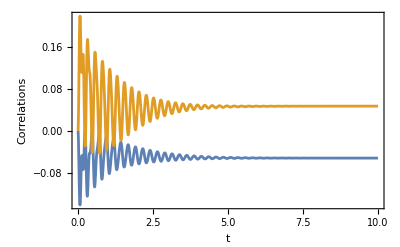

```mathematica
Plot[{Re[corr1n],Re[corr2n]},{t,0,10},Axes->False,Frame->True,FrameLabel->{Style["t", 20],Style["Correlations",20]},PlotRange->All]
```

We can also perform a spectroscopic analysis of the emission of two atom pairs by sweeping the detuning and evaluating the correlations ⟨σ_(2,1)^1σ_(1,2)^2+σ_(2,1)^2σ_(1,2)^1⟩  and ⟨σ_(2,1)^1σ_(1,2)^5+σ_(2,1)^5σ_(1,2)^1⟩

/150

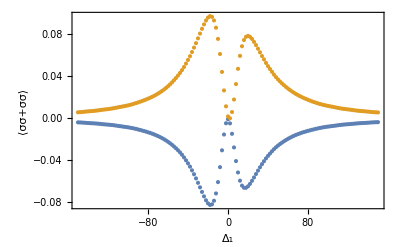

```mathematica
nd=150;
η0=SparseArray[{{1,1}->1},2];
rho0=KroneckerProduct[η0,η0,η0,η0,η0];
incon=InitialConditions[h,rho,rho0,t];
σ12=SparseArray[{{1,2}->1},2];
σ21=SparseArray[{{2,1}->1},2];
corr1=ExpectationValue[h,rho,KroneckerProduct[σ12,one,one,one,σ21]+KroneckerProduct[σ21,one,one,one,σ12]];
corr2=ExpectationValue[h,rho,KroneckerProduct[one,one,one,σ12,σ21]+KroneckerProduct[one,one,one,σ21,σ12]];
listplot1={};
listplot2={};
Print[Dynamic[jj],"/",nd]
Do[
det=-150+300jj/nd;
parmvals={Subscript[R, 1]->12.0,Subscript[Δ, 1]->det,ϕ->1.1,Subscript[γ, 1]->1.5,Subscript[γ, 1,2]->0.5,Subscript[Ω, 1]->0.7};
eqsn=eqs/.parmvals;
diffeq=Join[eqsn,incon];
sol=NDSolve[diffeq,Normal[rho],{t,0,10}][[1]];
corr1n=corr1/.sol/.{t->10};
corr2n=corr2/.sol/.{t->10};
AppendTo[listplot1,{det,corr1n}];
AppendTo[listplot2,{det,corr2n}];
,{jj,0,nd}]

ListPlot[{listplot1,listplot2},Axes->False,Frame->True,FrameLabel->{Style["Δ_1",20],Style["⟨σσ+σσ⟩",20]},PlotRange->All]
```

It is possible to abbreviate the process of obtaining the differential equations by using MasterEquation, which is a wrapper for LiouvilleMasterEquation, LiouvilleLindbladian, LiouvilleCommutator, and Ham

```mathematica
η0=SparseArray[{{1,1}->1},2]
rho0=KroneckerProduct[η0,η0,η0,η0,η0]
eqs=MasterEquation[h,rho,rho0,transCE,transdd,transLi,nl,na,t];
eqs[[{1,2,1025,1026}]]
```

SparseArray[…]

SparseArray[…]

{ρ_1'[t]==γ_1 ρ_2[t]-√2 Sin[4 ϕ-t Δ_1] R_1 ρ_3[t]-√2 Cos[4 ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_5[t]-√2 Sin[3 ϕ-t Δ_1] R_1 ρ_9[t]+γ_(1,2) ρ_11[t]-√2 Cos[3 ϕ-t Δ_1] R_1 ρ_13[t]+γ_(1,2) ρ_16[t]+γ_1 ρ_17[t]-√2 Sin[2 ϕ-t Δ_1] R_1 ρ_33[t]+γ_(1,2) ρ_41[t]-√2 Cos[2 ϕ-t Δ_1] R_1 ρ_49[t]+γ_(1,2) ρ_61[t]+γ_1 ρ_65[t]-√2 Sin[ϕ-t Δ_1] R_1 ρ_129[t]+γ_(1,2) ρ_161[t]-√2 Cos[ϕ-t Δ_1] R_1 ρ_193[t]+γ_(1,2) ρ_241[t]+γ_1 ρ_257[t]+√2 Sin[t Δ_1] R_1 ρ_513[t]+γ_(1,2) ρ_641[t]-√2 Cos[t Δ_1] R_1 ρ_769[t]+γ_(1,2) ρ_961[t],ρ_2'[t]==-γ_1 ρ_2[t]+√2 Sin[4 ϕ-t Δ_1] R_1 ρ_3[t]+√2 Cos[4 ϕ-t Δ_1] R_1 ρ_4[t]+γ_1 ρ_6[t]-√2 Sin[3 ϕ-t Δ_1] R_1 ρ_10[t]-1/2 γ_(1,2) ρ_11[t]-Ω_1 ρ_12[t]-√2 Cos[3 ϕ-t Δ_1] R_1 ρ_14[t]+Ω_1 ρ_15[t]-1/2 γ_(1,2) ρ_16[t]+γ_1 ρ_18[t]-√2 Sin[2 ϕ-t Δ_1] R_1 ρ_34[t]+γ_(1,2) ρ_42[t]-√2 Cos[2 ϕ-t Δ_1] R_1 ρ_50[t]+γ_(1,2) ρ_62[t]+γ_1 ρ_66[t]-√2 Sin[ϕ-t Δ_1] R_1 ρ_130[t]+γ_(1,2) ρ_162[t]-√2 Cos[ϕ-t Δ_1] R_1 ρ_194[t]+γ_(1,2) ρ_242[t]+γ_1 ρ_258[t]+√2 Sin[t Δ_1] R_1 ρ_514[t]+γ_(1,2) ρ_642[t]-√2 Cos[t Δ_1] R_1 ρ_770[t]+γ_(1,2) ρ_962[t],ρ_1[0]==1,ρ_2[0]==0}

Note that in this case the initial condition was set using rho0 in matrix form rather than as a list of coefficients.

## Optical pumping: the case of a many level atom

Optical pumping is the process by which resonant light redistributes the population of atomic energy levels, creating a non-equilibrium population distribution or spin polarization. We set up the master equation for a ^87 Rb atom in a four wave mixing configuration. We test the master equation under optical pumping conditions.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

We wish to generate the master equation for a single ^87 Rb atom, taking in to account the orbitals 5 S_(1/2), F=2; 5 P_(3/2), F=3 and 5 D_(3/2), F=3. We first obtain the configuration variables produced by TransitionLists. Jlist lists  the J value for each level. F list lists the F value for each level. mFlist are the ranges for the mF variable for each level. levtrlist indicates which levels are coupled by lasers. lasrtrlist indicates, for each laser, which levels it couples and the corresponding polarization vector.

```mathematica
na=1;
Jlist = {1/2,3/2,3/2};
Flist={2,3,3};
mFlist={Range[-2,2],Range[-3,3], Range[-3,3]};
levtrlist={{1,2},{2,3}};
lasertrlist={{{1,2},{1/(√2),-ⅈ/(√2),0}},{{2,3},{1/(√2),-ⅈ/(√2),0}}};
{levels, transitions, transdd, transLi, transCE}=TransitionLists[3/2,Jlist,Flist,mFlist,levtrlist,lasertrlist,na, R, δ,ϕ, γ, F, G];
```

At this point, it is helpful to inspect the variable levels, as this provides a clearer understanding of how the atomic orbitals are organized and how they factor into the master equation, nothing the first number is simply the position of the level on the list while the other numbers are actual quantum numbers.

```mathematica
levels
```

{{{1,-2,1/2,2},{2,-1,1/2,2},{3,0,1/2,2},{4,1,1/2,2},{5,2,1/2,2}},{{6,-3,3/2,3},{7,-2,3/2,3},{8,-1,3/2,3},{9,0,3/2,3},{10,1,3/2,3},{11,2,3/2,3},{12,3,3/2,3}},{{13,-3,3/2,3},{14,-2,3/2,3},{15,-1,3/2,3},{16,0,3/2,3},{17,1,3/2,3},{18,2,3/2,3},{19,3,3/2,3}}}

We may extract the number of levels from the the variable levels.

```mathematica
nl=levels[[-1,-1,1]]
```

19

We then set the matrix basis, define the density matrix and set the initial conditions so that the 5 orbitals of 5 S_(1/2)F=2 are equally occupied

```mathematica
h=MultiAtomBasis[nl,na]
n=Length[h]
rho=SparseArray[Table[ii->Subscript[ρ,ii][t],{ii,n}]]
rho0=SparseArray[Table[{ii,ii}->1/5,{ii,5}],{nl,nl}]
```

SparseArray[…]

361

SparseArray[…]

SparseArray[…]

We use MasterEquation to obtain the master equation and set the system parameters in the variable consts

```mathematica
diffeqs=MasterEquation[h,rho,rho0,transCE,transdd,transLi,nl,na,t];
consts={Subscript[γ, 1]->0.07573,Subscript[γ, 2]->0.001343,Subscript[R, 1]->0.1,Subscript[R, 2]->0.1,Subscript[δ, 1]->0.0,Subscript[δ, 2]->0.0,Subscript[ϕ, 1,1]->0,Subscript[ϕ, 2,1]->0};
diffeqsn=diffeqs/.consts;
```

The constants in consts correspond to ^87 Rb and are given in units of ns^-1. Finally, we solve the system of differential equations

```mathematica
tmax=100000;
sol=NDSolve[diffeqsn,Normal[rho],{t,0,tmax}][[1]];
```

We plot the populations of 5 S_(1/2), F=2; 5 P_(3/2), F=3 and 5 D_(3/2)F=3, confirming that optical pumping conditions are reached

```mathematica
groups={"5^2S^(1/2) F=2","5 PF=3", "5 DF=3"};
pl={};
con=0;
Do[
con+=1;
pops=Table[Subscript[ρ,ii][t],{ii,lev[[;;,1]]}]/.sol;
AppendTo[pl,Plot[pops,{t,0,tmax},PlotRange->All,Frame->True,Axes->False,FrameLabel->{Style["t (ns)",20],Style[groups[[con]],20]},PlotLabels->Table[StringJoin["m=",ToString[m]],{m,lev[[;;,2]]}]]];
,{lev,levels}];
GraphicsColumn[pl]
```

-Graphics-

#### Example

In order to distinguish the dynamics of all the populations, we repeat the previous example but  shift the polarization vectors slightly

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

We set the parameters and build the master equation (see previous example)

```mathematica
na=1;
Jlist = {1/2,3/2,3/2};
Flist={2,3,3};
mFlist={Range[-2,2],Range[-3,3], Range[-3,3]};
levtrlist={{1,2},{2,3}};

θ=0.5;
lasertrlist={{{1,2},{1/(√2),-ⅈ/(√2),0}Cos[θ]+{1/(√2),ⅈ/(√2),0}Sin[θ]},{{2,3},{1/(√2),-ⅈ/(√2),0}Cos[θ]+{1/(√2),ⅈ/(√2),0}Sin[θ]}};
{levels, transitions, transdd, transLi, transCE}=TransitionLists[3/2,Jlist,Flist,mFlist,levtrlist,lasertrlist,na, R, δ,ϕ, γ, F, G];

h=MultiAtomBasis[nl,na];
n=Length[h];
rho=SparseArray[Table[ii->Subscript[ρ,ii][t],{ii,n}]];
rho0=SparseArray[Table[{ii,ii}->1/5,{ii,5}],{nl,nl}];

diffeqs=MasterEquation[h,rho,rho0,transCE,transdd,transLi,nl,na,t];
consts={Subscript[γ, 1]->0.07573,Subscript[γ, 2]->0.001343,Subscript[R, 1]->0.1,Subscript[R, 2]->0.1,Subscript[δ, 1]->0.0,Subscript[δ, 2]->0.0,Subscript[ϕ, 1,1]->0,Subscript[ϕ, 2,1]->0};
diffeqsn=diffeqs/.consts;

tmax=100000;
sol=NDSolve[diffeqsn,Normal[rho],{t,0,tmax}][[1]];
```

When plotting the populations of 5 S_(1/2), F=2; 5 P_(3/2), F=3 and 5 D_(3/2)F=3, we confirm once again that the optical pumping conditions are fulfilled. However, orbitals that were unpopulated in the previous example now acquire a small population

```mathematica
groups={"5^2S^(1/2) F=2","5 PF=3", "5 DF=3"};
pl={};
con=0;
Do[
con+=1;
pops=Table[Subscript[ρ,ii][t],{ii,lev[[;;,1]]}]/.sol;
AppendTo[pl,Plot[pops,{t,0,tmax},PlotRange->All,Frame->True,Axes->False,FrameLabel->{Style["t (ns)",20],Style[groups[[con]],20]},PlotLabels->Table[StringJoin["m=",ToString[m]],{m,lev[[;;,2]]}]]];
,{lev,levels}];
GraphicsColumn[pl]
```

-Graphics-

## Superradiance

We illustrate the phenomenon of superradiance by comparing the spontaneous emission of a single atom with that of five coupled atoms. Superradiance is a collective quantum effect where a group of emitters radiate light much more intensely and faster than they would if each one emitted independently.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

For this example we employ five two-level atoms

```mathematica
na=5;
nl=2;
n = nl^na;
```

We set the matrix basis, density matrix and initial density matrix

```mathematica
h=MultiAtomBasis[nl,na];
rho=Table[Subscript[ρ,ii][t],{ii,1,n^2}];

η0={{0,0},{0,1}};
rho0=KroneckerProduct[η0,η0,η0,η0,η0];
```

The configuration files for the Hamiltonian and Lindbladian Liouville superoperators are defined such that all atoms are equally coupled. Two distinct atoms are assigned coupling parameters Mγ and Wγ for the Hamiltonian and Lindbladian Liouville superoperators, respectively. No self-coupling terms are included in the transdd part of the Hamiltonian. The configuration files are therefore specified as follows:

```mathematica
transCE={};
transLi={};
transdd={};
Do[
If[α==β,
AppendTo[transLi,{{1,2},{1,2},α,β,γ,0}];,
AppendTo[transLi,{{1,2},{1,2},α,β,W γ,0}];
AppendTo[transdd,{{1,2},{1,2},α,β,M γ,0}];
];
,{α,1,na},{β,1,na}];
```

At this point, we are ready to derive the master equation in terms of the differential equations for the density matrix coefficients (this might take some time)

```mathematica
diffeqs=MasterEquation[h,rho,rho0,transCE,transdd,transLi,nl,na,t];
```

For comparison, we first calculate the emission from five independent atoms. To this end, we set the coupling parameters to zero, compute the numerical form of the differential equations, and obtain the corresponding solution

```mathematica
consts={γ->0.151458,W->0.0,M->0.0};
diffeqsn=diffeqs/.consts;

tmin=0;
tmax=15;
sol=NDSolve[diffeqsn,rho,{t,tmin,tmax}][[1]];
```

The field of the emitted light contains the contributions from the five atoms E ∝ ∑_(α=1)^5 σ_(1,α) where σ_(1,α) denotes the atomic lowering operator  |1⟩_α_α⟨2| for atom α, hence E^†E, which is proportional to the emission power, is given by

```mathematica
EtE=Sum[SigmaT[{1,2},α,nl,na].Sigma[{1,2},β,nl,na],{α,na},{β,na}];
```

Using the solution we compute  ⟨E^†E⟩, the expected value of E^†E

```mathematica
evi=Re[ExpectationValue[h,rho,EtE]]/.sol;
```

We calculate a list of 50 time vs. emission power points and fit the list to I_0 exp(-t/τ) to obtain the decay time τ

```mathematica
nd=50;
datai=Table[{tmin+(tmax-tmin)ii/nd,evi/.{t->tmin+(tmax-tmin)ii/nd}},{ii,0,nd}];
fit=FindFit[datai,I0 Exp[- t/τ],{{I0,1},{τ,5}},t]
funi=I0 Exp[- t/τ]/.fit;
```

{I0→5.,τ→6.60249}

Note that τ = 1/γ = 6.60249

```mathematica
1/γ/.consts
```

6.60249

This is expected, since the atoms are independent. We plot the fitted function, the data points and the numerical solution for the expected value

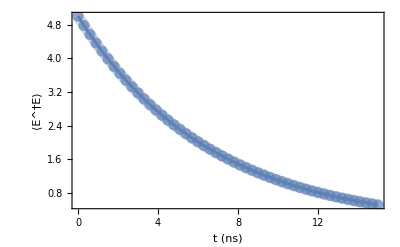

```mathematica
Show[{Plot[funi,{t,tmin,tmax},PlotStyle->{Thickness[0.02],Opacity[0.3]},Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["⟨E^†E⟩",20]}],Plot[evi,{t,tmin,tmax}],ListPlot[datai,PlotStyle->{Opacity[0.7],PointSize[0.02]}]}]
```

Now we calculate the emission of five strongly coupled atoms. To this end, we set the coupling parameters W and M to 0.752 and 0.45, compute the numerical form of the differential equations, and obtain the corresponding solution

```mathematica
consts={γ->0.151458,W->0.752,M->0.45};
diffeqsn=diffeqs/.consts;

sol=NDSolve[diffeqsn,rho,{t,tmin,tmax}][[1]];
```

Using the solution, we compute ⟨E^†E⟩, the expectation value of E^†E, which was obtained previously

```mathematica
evd=Re[ExpectationValue[h,rho,EtE]]/.sol;
```

We then calculate a list of 60 emission power  points as a function of time and again fit the list to I_0 exp(-t/τ) in order to extract the decay time  τ

```mathematica
nd=60;
datad=Table[{tmin+(tmax-tmin)ii/nd,evd/.{t->tmin+(tmax-tmin)ii/nd}},{ii,0,nd}];
fit=FindFit[datad[[15;;]],I0 Exp[- t/τ],{{I0,1},{τ,5}},t]
fund=I0 Exp[- t/τ]/.fit;
```

{I0→17.3229,τ→2.90696}

In this case, we used only the last 45 points, since the first 15 do not exhibit an exponential decay. Note that the decay time for coupled atoms is shorter. We plot the fitted function together with the data points and the numerical solution for the expectation value

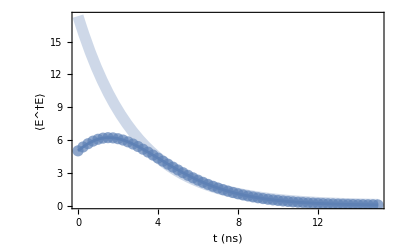

```mathematica
Show[{Plot[fund,{t,tmin,tmax},PlotStyle->{Thickness[0.02],Opacity[0.3]},Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["⟨E^†E⟩",20]},PlotRange->All],Plot[evd,{t,tmin,tmax},PlotRange->All],ListPlot[datad,PlotStyle->{Opacity[0.7],PointSize[0.02]}]}]
```

The emission curve exhibits the typical characteristics of superradiance: it starts at the same value as the emission from independent atoms, then rises to a maximum above the initial value, and finally decays twice as fast as in the independent case. Finally, both examples are plotted together for comparison

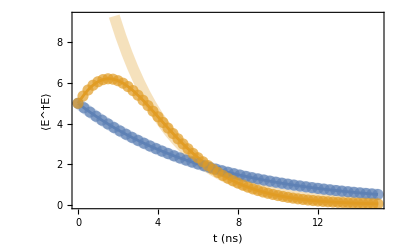

```mathematica
Show[{Plot[{funi,fund},{t,tmin,tmax},PlotStyle->{{Thickness[0.02],Opacity[0.3]},{Thickness[0.02],Opacity[0.3]}},Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["⟨E^†E⟩",20]}],Plot[{evi,evd},{t,tmin,tmax},PlotRange->All],ListPlot[{datai,datad},PlotStyle->{{Opacity[0.7],PointSize[0.02]},{Opacity[0.7],PointSize[0.02]}}]}]
```

## The dressed state evolution operator

We illustrate how to transform the solution of the master equation from the dressed-state basis to the standard-state basis for a system of two three-level atoms. This method provides a way to obtain the explicit form of the evolution operator. The resulting solution is shown to be consistent with that obtained directly from the master equation in the standard basis.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

We calculate the evolution operator for a system consisting of two (na=2) three level (nl=3) atoms interacting with two lasers with Rabi frequencies R_1 and R_2 and detunings  Δ_1 and Δ_2, respectively. The first laser couples the states |1⟩ and |2⟩ with  Rabi frequency R_1 and the second couples |2⟩ and |3⟩ with  Rabi frequency R_2 for both atoms. Both atoms are at different positions along the light-propagation direction and therefore have a phase difference ϕ. First we set the numerical values of the system parameters

```mathematica
parmvals={Subscript[R, 1]->12.0,Subscript[R, 2]->8.0,ϕ->0,Subscript[Δ, 1]->1.0,Subscript[Δ, 2]->-1.0,Subscript[γ, 1]->1.5, Subscript[γ, 2]->5.0,Subscript[γ, 1,1]->0.3,Subscript[γ, 2,2]->0.1,Subscript[Ω, 1]->0.7, Subscript[Ω, 2]->0.43}
```

{R_1→12.,R_2→8.,ϕ→0,Δ_1→1.,Δ_2→-1.,γ_1→1.5,γ_2→5.,γ_(1,1)→0.3,γ_(2,2)→0.1,Ω_1→0.7,Ω_2→0.43}

This is an important step because, although the evolution operator can be obtained symbolically for very sparse Liouville operators, in most cases it must be calculated numerically. The transCE configuration variable, which describes this light–matter interaction, is

```mathematica
transCE={{{1,2},1, Subscript[R, 1], Subscript[Δ, 1],0},{{1,2},2, Subscript[R, 1], Subscript[Δ, 1],0},{{2,3},1, Subscript[R, 2], Subscript[Δ, 2],ϕ},{{2,3},2, Subscript[R, 2], Subscript[Δ, 2],ϕ}}/.parmvals
```

{{{1,2},1,12.,1.,0},{{1,2},2,12.,1.,0},{{2,3},1,8.,-1.,0},{{2,3},2,8.,-1.,0}}

Assuming that the transitions |1⟩ → |2⟩ and |2⟩ → |3⟩ have distinct energy gaps and therefore do not couple to each other, the transdd variable is given by

```mathematica
transdd={{{1,2},{1,2},1,2,Subscript[Ω, 1],0},{{2,3}, {2,3},1,2,Subscript[Ω, 2],0},{{1,2},{1,2},2,1,Subscript[Ω, 1],0},{{2,3}, {2,3},2,1,Subscript[Ω, 2],0}}/.parmvals
```

{{{1,2},{1,2},1,2,0.7,0},{{2,3},{2,3},1,2,0.43,0},{{1,2},{1,2},2,1,0.7,0},{{2,3},{2,3},2,1,0.43,0}}

The only  transitions with non-vanishing dipole matrix elements are  |1⟩ →|2⟩ and |2⟩ →|3⟩. The transition  |1⟩ →|2⟩ is labeled as transition 1, and the transition  |2⟩ →|3⟩ is labeled as transition 2. The strengths of the corresponding decay rates are denoted accordingly: γ_1 is the rate due to the dipole element of the transition 1 if a single atom is involved, γ_(1,1) is the rate due to the dipole element of the transition 1 when two different atoms are involved,  γ_2 is the rate due to the dipole element of the transition 2 if a single atom is involved and γ_(2,2) is the rate due to the dipole element of the transition 2 when two different atoms are involved. The transLi configuration variable is thus given by

```mathematica
transLi={{{1,2},{1,2},1,1,Subscript[γ, 1],0},{{1,2},{1,2},2,2,Subscript[γ, 1],0},{{1,2},{1,2},1,2,Subscript[γ, 1,1],0},{{1,2},{1,2},2,1,Subscript[γ, 1,1],0},{{2,3},{2,3},1,1,Subscript[γ, 2],0},{{2,3},{2,3},2,2,Subscript[γ, 2],0},{{1,2},{1,2},1,2,Subscript[γ, 2,2],0},{{1,2},{1,2},2,1,Subscript[γ, 2,2],0}}/.parmvals
```

{{{1,2},{1,2},1,1,1.5,0},{{1,2},{1,2},2,2,1.5,0},{{1,2},{1,2},1,2,0.3,0},{{1,2},{1,2},2,1,0.3,0},{{2,3},{2,3},1,1,5.,0},{{2,3},{2,3},2,2,5.,0},{{1,2},{1,2},1,2,0.1,0},{{1,2},{1,2},2,1,0.1,0}}

```mathematica
nl= 3;
na =2;
rho=SparseArray[Table[{ii}->Subscript[ρ, ii][t],{ii,nl^(2na)}]]
h = MultiAtomBasis[nl,na]
```

SparseArray[…]

SparseArray[…]

Calculate the dressed state Hamiltonian and the corresponding Liouville operator

```mathematica
hamd=HamDressed[transCE, transdd, nl, na];
LiouvilleHR = -CleanUp[LiouvilleCommutator[h,hamd]];
```

Calculate the Lindbladian superoperator

```mathematica
LiouvilleL=CleanUp[LiouvilleLindbladian[h, transLi,nl,na]];
```

It is important to remember that the Lindbladian superoperator remains invariant under rotating-frame transformations and, therefore, is calculated just as it would be in the standard basis. The full Liouville operator is the sum of LiouvilleHR and LiouvilleL

```mathematica
LiouvilleR=Re[Developer`ToPackedArray@(LiouvilleHR+LiouvilleL)];
```

```mathematica
VRD=MatrixExp[LiouvilleR t];
```

Obtain the rotating-frame transformations

```mathematica
{U, UT,UR, URT} = RotatingFrameTrans[h,transCE,nl, na, t]
```

{SparseArray[…],SparseArray[…],SparseArray[<225>, {81, 81}],SparseArray[<225>, {81, 81}]}

and use them to convert the results from the rotating frame to the standard basis

```mathematica
ρ0=SparseArray[{1,1}->1,9];
rhot=URT.VRD.UR.Proj[h,ρ0];
```

To illustrate the procedure for calculating expectation values, we construct the operator op  =  |1⟩⟨2|⊗1+ |2⟩⟨1|⊗1, and then evaluate its expectation value

```mathematica
op=KroneckerProduct[SparseArray[{1,2}->1,3],IdentityMatrix[3]]+KroneckerProduct[SparseArray[{2,1}->1,3],IdentityMatrix[3]];
rexpval = ExpectationValue[h,rhot,op];
```

To compare, we also find the system’s evolution through the master equation

```mathematica
eqs=MasterEquation[h,rho,ρ0,transCE,transdd,transLi,nl,na,t];
```

and numerically solve the differential equations

```mathematica
sol=NDSolve[eqs,Normal[rho],{t,0,10.0}];
```

and find the expectation value of op using this solution

```mathematica
expval=ExpectationValue[h,rho,op]/.sol;
```

Superimpose the solutions obtained from the dressed state and the standard basis

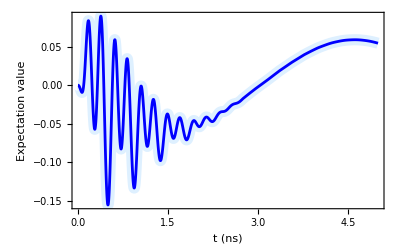

```mathematica
Plot[{Re[rexpval],Re[expval]},{t,0,5},PlotRange->All,Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["Expectation value",20]},PlotStyle->{Directive[Thickness[0.02],LightBlue],Directive[Thickness[0.005],Blue]}]
```

## Time evolution of transmons

To illustrate the use of LiouvilleLindbladianFromLindbladOperators and LiouvilleDaggerLindbladianFromLindbladOperators in obtaining the dynamics of an arbitrary system, we analyze the time evolution of a transmon subject to both a coherent drive and dissipative mechanisms.

"Content"

#### Example

Load MultiAtomLiouvilleEquationGenerator

```mathematica
SetDirectory[PathToMultiAtomLiouvilleEquationGenerator];
Needs["MultiAtomLiouvilleEquationGenerator`"]
```

The Hamiltonian of a transmon qubit is given by H = ℏ ω (a^†a +1/2) + α/12(a^†+ a)^4+λ(t) (a^†+ a) where a^†and a are the usual creation and annihilation operators, ω is the transmon frequency, α is the anharmonicity parameter and λ(t) represents the drive. We assume that the transmon is coupled to a thermal bath, which is modeled by the Lindbladian L = -γ/2({a^†a, ρ}-2aρ a^†). To build the Hamiltonian and Lindbladian we define the creation and annihilation operators

```mathematica
aop[ns_]:=SparseArray[Table[{n+1,n}->√n,{n,1,ns-1}],ns];
dop[ns_]:=SparseArray[Table[{n+1,n+2}->√(n+1),{n,0,ns-2}],ns];
```

where ns is the number of states. We analyze the behaviour of the first 8 states of a transmon. We thus start by generating a matrix basis with 8 states with

```mathematica
h=MultiAtomBasis[8,1]
```

SparseArray[…]

We also define the creation and annihilation operators for such a number of states and a SparseArray called one for the unitary matrix

```mathematica
ns=8;
a=dop[ns];
at=aop[ns];
one=SparseArray[Table[{ii,ii}->1,{ii,1,ns}]];
```

The Hamiltonian is thus given by

```mathematica
H=ℏ ω (at.a+1/2 one)-α/12(a+at).(a+at).(a+at).(a+at)+ λ (a+at);
```

We set the constants of the system

```mathematica
consts={ℏ->1.0,ω->4.5,α->-0.30,λ->0}
```

{ℏ→1.,ω→4.5,α→-0.3,λ→0}

and calculate the eigenvalues of H in order to know the excitation energy Δ between the ground and the first excited states

```mathematica
Hn=Normal[H]/.consts;
eval=Eigenvalues[Hn]
Δ=eval[[7]]-eval[[8]]
```

{37.2165,35.0278,28.4791,22.6551,17.3162,12.0971,7.08815,2.31999}

4.76816

We calculate the Liouville operator for the Hamiltonian

```mathematica
LiH=CleanUp[-LiouvilleCommutator[h,H]]
```

SparseArray[…]

The Lindbladian Liouville operator is calculated from just one Lindblad operator, namely a, and just one decay coefficient γ

```mathematica
liops = SparseArray[{a}]
gammas = SparseArray[{γ}]
LiL =LiouvilleLindbladianFromLindbladOperators[h,liops, gammas]
```

SparseArray[…]

SparseArray[…]

SparseArray[…]

Compute the overall Liouville operator and build the differential equations

```mathematica
Li=CleanUp[LiH+LiL]
```

SparseArray[…]

Build the system of differential equations for the density matrix coefficients

```mathematica
rho=Table[Subscript[ρ, ii][t],{ii,Length[h]}];
eqs=LiouvilleMasterEquation[rho, Li, t];
```

We reset the consts variable to include the decay coefficient γ and a drive with frequency Δ that excites the transition from the ground state to the first excited state. We then evaluate the equations with these updated constants and set the initial conditions such that the transmon starts in the ground state. Finally, the initial conditions are combined with the equations.

```mathematica
consts={ℏ->1.0,ω->4.5,α->-0.30,λ->0.1 Sin[Δ t],γ->0.02}
eqsn=eqs/.consts;
inconds=Table[Subscript[ρ, ii][0]==KroneckerDelta[ii,1],{ii,Length[h]}];
difeqs=Join[eqsn,inconds];
```

{ℏ→1.,ω→4.5,α→-0.3,λ→0.1 Sin[4.76816 t],γ→0.02}

Solve the differential equations

```mathematica
sol=NDSolve[difeqs,rho,{t,0,100}][[1]];
```

Calculate and plot the populations of the 8 transmon quantum levels

```mathematica
plots={};
Do[
op=SparseArray[{{ii,ii}->1},ns];
expval=ExpectationValue[h,rho,op];
expvaln=expval/.sol;
AppendTo[plots,expvaln];
,{ii,1,8}]
```

```mathematica
Plot[plots,{t,0,32},PlotRange->All,Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["Populations",20]},PlotLabels->Table[Style[Subscript[ρ, ii],16],{ii,1,8}],ImageSize->450]
```

-Graphics-

We observe that as the ground state (blue) is gradually depopulated, the first excited state (orange) becomes populated due to the driving field. In addition, a small fraction of the population leaks into the higher excited states (green and subsequent levels), reflecting the multi-level structure of the transmon and the fact that the drive is not perfectly restricted to a two-level subspace.